## Introduction

```mathematica
SetDirectory[NotebookDirectory[]];
Clear[qetb,qets,qetb1,qetb2,qetbp1,qetbp2,qets2,qetsp2,ft,ft1,ft2,ftp1,ftp2];
s=12000;
sa=1/3;
s1=s*sa; 
nh=12000;
nl=15000;
g=sa/(1-sa);
```

```mathematica
Solve[(nh*alphah+nl*alphal)/(nh+nl)==10&&alphah/alphal==dgr,{alphah,alphal}]
```

{{alphah→(90 dgr)/(5+4 dgr),alphal→90/(5+4 dgr)}}

```mathematica
N[{41067/17059840,369603/213248000}]
```

{0.00240723,0.00173321}

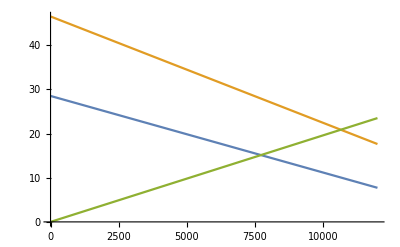

```mathematica
Clear[bh,bl,ah,al];
dgr=7;
alpha=(90*dgr)/(4+5 dgr);
beta=39/64*alpha;(*marginal schedule delay cost of arriving early*)
gamma=1521/10/64*alpha;(*marginal schedule delay cost of arriving late*)
h=beta*gamma/(beta+gamma)/s1; (*marginal congestion cost for high type*)
l=h/dgr;(*marginal congestion cost for low type,9/10*h*)
bh=41067/17059840;
bl=369603/213248000;
ah=bh*nh+h*(nh+nl)*sa;
al=bl*nl+l*(nh+nl)*sa;
Plot[{al-bl*x,ah-bh*x,h*x},{x,0,12000}]
```

## Bertrand competition and flat tolls (fixed slopes)

```mathematica
degreeft[dgr_]:=(*vary the ration of h/l, but keep the slopes unchanged*)Module[{h,l,n,m,m1,m2,m3,m4,m5,alpha,beta,gamma,bh,bl,ah,al,nh1,nh2,nl1,nl2,pi1,pi2,sw,eh,el,c,ph,pl,csh,csl,tau1,tau2,tau1n,tau2n,idc,rfprpu,rfprpr,rfzz,rfo,rfm,rfzpr,rfzpu,rfstb,rfstbp,min,max,ss,a,list,mtrxft},
alpha=(90*dgr)/(4+5 dgr);
beta=39/64*alpha;(*marginal schedule delay cost of arriving early*)
gamma=1521/10/64*alpha;(*marginal schedule delay cost of arriving late*)
h=beta*gamma/(beta+gamma)/s1; (*marginal congestion cost for high type*)
l=h/dgr;(*marginal congestion cost for low type,9/10*h*)
(*The slopes of the demand curve does not change, only the intercept changes*)
bh=41067/17059840;
bl=369603/213248000;
ah=bh*nh+h*(nh+nl)*sa;(*because h and l changes, to keep nh and nl unchanged, ah and al must also change. So ah increases but al decreases*)
al=bl*nl+l*(nh+nl)*sa;
ft[tau1_,tau2_]:=(*ft calculates the equilibrium given flat tolls*)
Module[{nh1,nh2,nl1,nl2,m1,pi1,pi2,sw,eh,el,c,ph,pl,csh,csl},
pi1=-tau1*(nh1+nl1);
pi2=-tau2*(nh2+nl2);
sw=-ah*(nh1+nh2)+bh*(nh1+nh2)^2/2-al*(nl1+nl2)+bl*(nl1+nl2)^2/2+h*(nh1+nl1)*nh1+l*(nh1+nl1)*nl1+h*g*(nh2+nl2)*nh2+l*g*(nh2+nl2)*nl2;
csh=ah*(nh1+nh2)-bh*(nh1+nh2)^2/2-(h*nh1+h*nl1+tau1)*nh1-(h*g*nh2+h*g*nl2+tau2)*nh2;
csl=al*(nl1+nl2)-bl*(nl1+nl2)^2/2-(l*nh1+l*nl1+tau1)*nl1-(l*g*nh2+l*g*nl2+tau2)*nl2;
ph=ah-bh*(nh1+nh2);
pl=al-bl*(nl1+nl2);
m1=Minimize[0,
{nh1*(ah-bh*(nh1+nh2)-h*nh1-h*nl1-tau1)==0,nh2*(ah-bh*(nh1+nh2)-h*g*nh2-h*g*nl2-tau2)==0,nl1*(al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1)==0,nl2*(al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2)==0,ah-bh*(nh1+nh2)-h*nh1-h*nl1-tau1≤0,ah-bh*(nh1+nh2)-h*g*nh2-h*g*nl2-tau2≤0,al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1≤0,al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2≤0,
nh1≥0,nh2≥0,nl1≥0,nl2>=0},
{nh1,nh2,nl1,nl2}][[2]];
{nh1,nh2,nl1,nl2,pi1,pi2,sw,tau1,tau2,ph,pl,csh,csl}/.m1
];
ft1[tau2_]:=(*ft1 calculates the best response for private supplier on link 1*)
Module[{nh1,nh2,nl1,nl2,m2,tau1},
m2=Minimize[-tau1*(nh1+nl1),
{nh1*(ah-bh*(nh1+nh2)-h*nh1-h*nl1-tau1)==0,nh2*(ah-bh*(nh1+nh2)-h*g*nh2-h*g*nl2-tau2)==0,nl1*(al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1)==0,nl2*(al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2)==0,ah-bh*(nh1+nh2)-h*nh1-h*nl1-tau1≤0,ah-bh*(nh1+nh2)-h*g*nh2-h*g*nl2-tau2≤0,al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1≤0,al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2≤0,
nh1≥0,nh2≥0,nl1≥0,nl2≥0},{nh1,nh2,nl1,nl2,tau1}][[2]];
{tau1}/.m2
];
ft2[tau1_]:=(*ft2 calculates the best response for private supplier on link 2*)
Module[{nh1,nh2,nl1,nl2,m3,tau2},
m3=Minimize[-tau2*(nh2+nl2),
{nh1*(ah-bh*(nh1+nh2)-h*nh1-h*nl1-tau1)==0,nh2*(ah-bh*(nh1+nh2)-h*g*nh2-h*g*nl2-tau2)==0,nl1*(al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1)==0,nl2*(al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2)==0,ah-bh*(nh1+nh2)-h*nh1-h*nl1-tau1≤0,ah-bh*(nh1+nh2)-h*g*nh2-h*g*nl2-tau2≤0,al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1≤0,al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2≤0,
nh1≥0,nh2≥0,nl1≥0,nl2≥0},{nh1,nh2,nl1,nl2,tau2}][[2]];
{tau2}/.m3
];
ftp1[tau2_]:=(*ftp1 calculates the best response for social planner on link 1*)
Module[{nh1,nh2,nl1,nl2,m4,tau1,sw},
sw=-ah*(nh1+nh2)+bh*(nh1+nh2)^2/2-al*(nl1+nl2)+bl*(nl1+nl2)^2/2+h*(nh1+nl1)*nh1+l*(nh1+nl1)*nl1+h*g*(nh2+nl2)*nh2+l*g*(nh2+nl2)*nl2;
m4=Minimize[sw,
{nh1*(ah-bh*(nh1+nh2)-h*nh1-h*nl1-tau1)==0,nh2*(ah-bh*(nh1+nh2)-h*g*nh2-h*g*nl2-tau2)==0,nl1*(al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1)==0,nl2*(al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2)==0,ah-bh*(nh1+nh2)-h*nh1-h*nl1-tau1≤0,ah-bh*(nh1+nh2)-h*g*nh2-h*g*nl2-tau2≤0,al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1≤0,al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2≤0,
nh1≥0,nh2≥0,nl1≥0,nl2≥0},{nh1,nh2,nl1,nl2,tau1}][[2]];
{tau1}/.m4
];
ftp2[tau1_]:=(*ftp2 calculates the best response for social planner on link 2*)
Module[{nh1,nh2,nl1,nl2,m5,tau2,sw},
sw=-ah*(nh1+nh2)+bh*(nh1+nh2)^2/2-al*(nl1+nl2)+bl*(nl1+nl2)^2/2+h*(nh1+nl1)*nh1+l*(nh1+nl1)*nl1+h*g*(nh2+nl2)*nh2+l*g*(nh2+nl2)*nl2;
m5=Minimize[sw,
{nh1*(ah-bh*(nh1+nh2)-h*nh1-h*nl1-tau1)==0,nh2*(ah-bh*(nh1+nh2)-h*g*nh2-h*g*nl2-tau2)==0,nl1*(al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1)==0,nl2*(al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2)==0,ah-bh*(nh1+nh2)-h*nh1-h*nl1-tau1≤0,ah-bh*(nh1+nh2)-h*g*nh2-h*g*nl2-tau2≤0,al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1≤0,al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2≤0,
nh1≥0,nh2≥0,nl1≥0,nl2≥0},{nh1,nh2,nl1,nl2,tau2}][[2]];
{tau2}/.m5
];
(*Private-Public*)
tau1=10;
tau2=10;
tau1n=tau1;
tau2n=tau2;
idc=1;
While[idc>10^-5,
tau1n=ft1[tau2n][[1]];(*toll 1 is private*)
tau2n=ftp2[tau1n][[1]];(*toll 2 is public*)
idc=Max[Abs[tau2n-tau2],Abs[tau1n-tau1]];
tau1=tau1n;
tau2=tau2n;
Print[N[ft[tau1,tau2]],N[idc]];
];
rfprpu=ft[tau1,tau2];
Print["private-public:", N[rfprpu]];
(*(*Private-Private*)
idc=1;
While[idc>10^-5,
tau1n=ft1[tau2n][[1]];
tau2n=ft2[tau1n][[1]];
idc=Max[Abs[tau2n-tau2],Abs[tau1n-tau1]];
tau1=tau1n;
tau2=tau2n;
Print[N[ft[tau1,tau2]],N[idc]];
];
rfprpr=ft[tau1,tau2];
Print["private-private:", N[rfprpr]];*)
(*Free-Free*)
tau1=0;tau2=0;
rfzz=ft[tau1,tau2];
Print["free-free:", N[rfzz]];
(*public-public*)
Clear[tau1,tau2,m];m=Minimize[-ah*(nh1+nh2)+bh*(nh1+nh2)^2/2-al*(nl1+nl2)+bl*(nl1+nl2)^2/2+h*(nh1+nl1)*nh1+l*(nh1+nl1)*nl1+h*g*(nh2+nl2)*nh2+l*g*(nh2+nl2)*nl2,{nh1*(ah-bh*(nh1+nh2)-h*nh1-h*nl1-tau1)==0,nh2*(ah-bh*(nh1+nh2)-h*g*nh2-h*g*nl2-tau2)==0,nl1*(al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1)==0,nl2*(al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2)==0,ah-bh*(nh1+nh2)-h*nh1-h*nl1-tau1≤0,ah-bh*(nh1+nh2)-h*g*nh2-h*g*nl2-tau2≤0,al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1≤0,al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2≤0,nh1≥0,nh2≥0,nl1≥0,nl2≥0},{nh1,nh2,nl1,nl2,tau1,tau2}][[2]];
rfo=ft[tau1/.m,tau2/.m];
Print["public-public:", N[rfo]];
(*Monopoly*)
Clear[tau1,tau2,m];
m=Minimize[-tau1*(nh1+nl1)-tau2*(nh2+nl2),{nh1*(ah-bh*(nh1+nh2)-h*nh1-h*nl1-tau1)==0,nh2*(ah-bh*(nh1+nh2)-h*g*nh2-h*g*nl2-tau2)==0,nl1*(al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1)==0,nl2*(al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2)==0,ah-bh*(nh1+nh2)-h*nh1-h*nl1-tau1≤0,ah-bh*(nh1+nh2)-h*g*nh2-h*g*nl2-tau2≤0,al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1≤0,al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2≤0,nh1≥0,nh2≥0,nl1≥0,nl2≥0},{nh1,nh2,nl1,nl2,tau1,tau2}][[2]];
rfm=ft[tau1/.m,tau2/.m];
Print["Monopoly:", N[rfm]];
(*free-Public*)
tau1=0;
tau2=ftp2[tau1][[1]];
rfzpu=ft[tau1,tau2];
Print["free-Public:", N[rfzpu]];
(*free-Private*)
tau1=0;
tau2=ft2[tau1][[1]];
rfzpr=ft[tau1,tau2];
Print["free-private:", N[rfzpr]];
(*(*Stackelberg-public*)
idc=1;
ss=5;
min=0;
max=Max[ah,al];
While[idc>10^-6,
list=ParallelTable[ft[ft1[tau2][[1]],tau2][[7]],{tau2,min,max,(max-min)/ss}];
a=Position[list,Min[list]][[1]][[1]];
min=min+(max-min)*(a-2)/ss;
max=min+(max-min)*a/ss;
idc=max-min;
(*Print[a];*)
];
tau2=min;
rfstb=ft[ft1[tau2][[1]],tau2];
Print["Stackelberg Public:", N[rfstb]];*)
(*Stackelberg-private*)
idc=1;
ss=3;
min=0;
max=Max[ah,al];
While[idc>10^-6,
list=ParallelTable[ft[ft1[tau2][[1]],tau2][[6]],{tau2,min,max,(max-min)/ss}];
a=Position[list,Min[list]][[1]][[1]];
min=min+(max-min)*(a-2)/ss;
max=min+(max-min)*a/ss;
idc=max-min;
(*Print[a];*)
];
tau2=min;
rfstbp=ft[ft1[tau2][[1]],tau2];
Print["Stackelberg Private:", N[rfstbp]];
mtrxft=MapThread[Prepend,{Prepend[Transpose[N[{rfstbp,rfzz,rfo,rfm,rfzpu,rfzpr,rfprpu},6]],{"Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}],{dgr "Flat toll","nh1","nh2","nl1","nl2","pi1","pi2","sw","tau1","tau2","price h","price l","cs h","cs l"}}]
]
```

```mathematica
cft=ParallelMap[degreeft,{1,2,3,4,5,6,7}];
Export["degreeftslope.xls",cft,"XLS"]
```

Needs::nocont: Context "PacletManager`" was not created when Needs was evaluated.

{6287.81,2807.21,0.,10965.3,-64648.5,-131609.,-400019.,10.2816,9.55591,17.9057,17.9057,99562.6,104199.}0.444089

{0.,10392.4,10154.8,136.695,-76136.1,-108516.,-406431.,7.49754,10.3063,19.3775,13.33,129993.,91786.2}2.50246

{0.,10683.9,10022.9,0.,-82602.8,-107383.,-414431.,8.2414,10.0509,20.1019,12.013,137387.,87058.}1.7586

{0.,10654.1,9812.98,0.,-85988.2,-111166.,-417226.,8.7627,10.4341,20.8682,11.5085,136622.,83449.2}1.2373

{6342.51,2782.56,0.,11007.,-64331.5,-130632.,-400179.,10.1429,9.47324,17.8334,17.8334,100221.,104993.}0.138635

{0.,10360.8,10096.9,142.017,-76958.7,-109282.,-406294.,7.62205,10.4051,19.4536,13.4212,129203.,90849.9}0.124501

{0.,10683.9,9995.18,0.,-82959.,-107383.,-414306.,8.2999,10.0509,20.1019,12.0611,137387.,86576.8}0.058506

{0.,10654.1,9572.85,0.,-88511.4,-111166.,-415715.,9.24608,10.4341,20.8682,11.9247,136622.,79415.1}0.483377

{6352.69,2777.97,0.,11014.8,-64270.8,-130450.,-400207.,10.1171,9.45785,17.8199,17.8199,100344.,105142.}0.0258077

{6354.58,2777.12,0.,11016.3,-64259.5,-130416.,-400212.,10.1123,9.45499,17.8174,17.8174,100367.,105169.}0.00480424

{0.,10683.9,9995.18,0.,-82959.,-107383.,-414306.,8.2999,10.0509,20.1019,12.0611,137387.,86576.8}0.

{0.,10654.1,9572.85,0.,-88511.4,-111166.,-415715.,9.24608,10.4341,20.8682,11.9247,136622.,79415.1}0.

{0.,10350.6,10078.2,143.733,-77220.8,-109528.,-406247.,7.66219,10.4369,19.4782,13.4507,128949.,90549.}0.0401468

private-public:{0.,10683.9,9995.18,0.,-82959.,-107383.,-414306.,8.2999,10.0509,20.1019,12.0611,137387.,86576.8}

private-public:{0.,10654.1,9572.85,0.,-88511.4,-111166.,-415715.,9.24608,10.4341,20.8682,11.9247,136622.,79415.1}

free-free:{9000.,3000.,0.,15000.,0.,0.,-368307.,0.,0.,16.9336,3.38673,173321.,194986.}

free-free:{9000.,3000.,0.,15000.,0.,0.,-368307.,0.,0.,17.6283,2.51834,173321.,194986.}

{6354.94,2776.96,0.,11016.5,-64257.4,-130410.,-400213.,10.1114,9.45445,17.817,17.817,100371.,105174.}0.000894334

{0.,10347.3,10072.1,144.286,-77305.1,-109608.,-406232.,7.67514,10.4472,19.4861,13.4601,128867.,90452.}0.0129458

{6355.,2776.93,0.,11016.6,-64257.,-130409.,-400213.,10.1112,9.45435,17.8169,17.8169,100372.,105175.}0.000166485

{6355.02,2776.93,0.,11016.6,-64256.9,-130408.,-400213.,10.1112,9.45434,17.8169,17.8169,100372.,105175.}0.0000309921

{0.,10346.2,10070.2,144.465,-77332.2,-109633.,-406227.,7.67931,10.4505,19.4886,13.4632,128841.,90420.8}0.00417454

{6355.02,2776.92,0.,11016.6,-64256.9,-130408.,-400213.,10.1112,9.45433,17.8169,17.8169,100372.,105176.}5.76934×10^-6

private-public:{6355.02,2776.92,0.,11016.6,-64256.9,-130408.,-400213.,10.1112,9.45433,17.8169,17.8169,100372.,105176.}

free-free:{9000.,3000.,0.,15000.,0.,0.,-368307.,0.,0.,10.9128,10.9128,173321.,194986.}

public-public:{6996.96,2487.59,0.,11506.3,-59362.4,-118725.,-401095.,8.48403,8.48403,16.9681,16.9681,108273.,114734.}

Monopoly:{4500.,1848.84,0.,7151.16,-85770.3,-171541.,-350143.,19.0601,19.0601,24.5164,24.5164,48515.,44317.4}

{0.,10345.9,10069.6,144.522,-77340.9,-109641.,-406225.,7.68066,10.4516,19.4894,13.4642,128832.,90410.7}0.00134613

free-Public:{10344.,979.029,0.,14059.8,0.,-51506.6,-377131.,0.,3.42492,12.5424,12.5424,154317.,171307.}

free-private:{8988.8,953.677,4096.,8046.32,0.,-93684.1,-340433.,0.,10.4093,15.8657,15.8657,118981.,127769.}

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

{0.,10345.8,10069.4,144.541,-77343.7,-109644.,-406225.,7.68109,10.4519,19.4897,13.4645,128830.,90407.5}0.000434076

public-public:{0.,10683.9,11821.,0.,-52583.2,-107383.,-418449.,4.44828,10.0509,20.1019,8.89657,137387.,121096.}

public-public:{0.,10654.1,12437.2,0.,-43282.8,-111166.,-425121.,3.48011,10.4341,20.8682,6.96022,136622.,134049.}

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

{0.,10345.8,10069.3,144.547,-77344.7,-109645.,-406225.,7.68123,10.452,19.4898,13.4646,128829.,90406.4}0.000139973

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable :: subpar will be suppressed during this calculation.

{0.,10345.7,10069.3,144.549,-77344.9,-109645.,-406225.,7.68128,10.4521,19.4898,13.4646,128828.,90406.1}0.000045136

Monopoly:{122.591,7274.39,6821.14,0.,-103805.,-154004.,-363987.,14.9494,21.1707,28.0142,17.5624,65856.2,40321.3}

Monopoly:{258.488,7194.3,6919.89,0.,-104189.,-154885.,-367424.,14.5142,21.5288,28.5746,16.5228,66853.7,41497.2}

free-Public:{0.,10683.9,13929.7,0.,0.,-107383.,-412922.,0.,10.0509,20.1019,5.24179,137387.,168153.}

free-Public:{0.,10654.1,14166.,0.,0.,-111166.,-421694.,0.,10.4341,20.8682,3.96386,136622.,173906.}

{0.,10345.7,10069.3,144.549,-77345.,-109645.,-406225.,7.68129,10.4521,19.4898,13.4647,128828.,90406.}0.0000145546

free-private:{0.,8146.9,13929.7,0.,0.,-151082.,-399121.,0.,18.5447,26.2089,5.24179,79886.5,168153.}

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

free-private:{0.,7796.57,14166.,0.,0.,-156800.,-403869.,0.,20.1114,27.747,3.96386,73163.5,173906.}

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

{0.,10345.7,10069.3,144.549,-77345.1,-109645.,-406225.,7.6813,10.4521,19.4898,13.4647,128828.,90405.9}4.69332×10^-6

private-public:{0.,10345.7,10069.3,144.549,-77345.1,-109645.,-406225.,7.6813,10.4521,19.4898,13.4647,128828.,90405.9}

free-free:{9000.,3000.,0.,15000.,0.,0.,-368307.,0.,0.,15.5076,5.16921,173321.,194986.}

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable :: subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable :: subpar will be suppressed during this calculation.

public-public:{0.,10726.1,10766.3,80.537,-66576.,-100113.,-407123.,6.18372,9.26402,18.5743,12.3674,138474.,101960.}

Monopoly:{0.,7107.99,6644.16,0.,-105214.,-150406.,-354686.,15.8355,21.1601,27.2839,19.6516,60810.9,38256.1}

free-Public:{0.,10748.5,13506.6,0.,0.,-99532.8,-396679.,0.,9.26019,18.5204,7.75761,139053.,158093.}

free-private:{0.,8774.23,13506.6,0.,0.,-137874.,-388630.,0.,15.7135,23.2728,7.75761,92663.,158093.}

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable :: subpar will be suppressed during this calculation.

Stackelberg Private:{7250.97,837.492,0.,9567.31,-83652.5,-145882.,-387603.,11.5367,14.0207,20.3288,20.3288,78744.5,79323.2}

{0.,9744.44,8087.33,2481.57,-67864.3,-121409.,-400363.,8.39144,9.9304,19.4604,14.6954,114288.,96801.}1.60856

{0.,9750.78,8098.97,2479.76,-67750.5,-121224.,-400393.,8.36533,9.91159,19.4451,14.6783,114437.,96981.1}0.0261108

{0.,9752.5,8102.11,2479.27,-67719.6,-121174.,-400401.,8.35827,9.90651,19.441,14.6737,114477.,97029.8}0.00705539

{0.,9752.96,8102.96,2479.14,-67711.3,-121161.,-400403.,8.35637,9.90513,19.4399,14.6725,114488.,97043.}0.00190644

{0.,9753.09,8103.19,2479.1,-67709.,-121157.,-400404.,8.35585,9.90476,19.4396,14.6722,114491.,97046.6}0.000515138

{0.,9753.12,8103.25,2479.09,-67708.4,-121156.,-400404.,8.35571,9.90466,19.4395,14.6721,114492.,97047.5}0.000139195

{0.,9753.13,8103.27,2479.09,-67708.3,-121156.,-400404.,8.35567,9.90463,19.4395,14.672,114492.,97047.8}0.000037612

{0.,9753.13,8103.27,2479.09,-67708.2,-121156.,-400404.,8.35566,9.90463,19.4395,14.672,114492.,97047.8}0.0000101631

{0.,9753.13,8103.27,2479.09,-67708.2,-121156.,-400404.,8.35566,9.90462,19.4395,14.672,114492.,97047.9}2.74618×10^-6

private-public:{0.,9753.13,8103.27,2479.09,-67708.2,-121156.,-400404.,8.35566,9.90462,19.4395,14.672,114492.,97047.9}

free-free:{9000.,3000.,0.,15000.,0.,0.,-368307.,0.,0.,14.0307,7.01536,173321.,194986.}

public-public:{0.,10120.8,8777.83,2374.39,-60059.5,-110139.,-401267.,6.84218,8.81444,18.5543,13.6844,123288.,107781.}

Monopoly:{0.,6733.81,6569.34,0.,-108438.,-144499.,-344914.,16.5067,21.4588,26.7077,21.6274,54577.1,37399.4}

free-Public:{0.,11783.2,11827.4,1901.05,0.,-53176.,-383619.,0.,3.88593,14.5526,9.21926,167115.,163329.}

free-private:{220.989,9000.,13070.1,0.,0.,-123346.,-373726.,0.,13.7051,20.7205,10.3602,102339.,148040.}

Stackelberg Private:{0.,7500.59,6964.85,0.,-102330.,-155326.,-367409.,14.6924,20.7085,27.7648,17.3133,67714.1,42038.2}

Stackelberg Private:{0.,7637.52,7082.99,0.,-100991.,-157715.,-372391.,14.2582,20.65,28.1298,16.2402,70209.,43476.5}

{0.,10666.7,9901.92,0.,-84627.2,-109556.,-416097.,8.54654,10.2709,20.5417,11.7247,136945.,84968.8}1.45346

{0.,10666.7,9753.09,0.,-86337.,-109556.,-415271.,8.85228,10.2709,20.5417,11.9827,136945.,82433.7}0.305731

{0.,10666.7,9753.09,0.,-86337.,-109556.,-415271.,8.85228,10.2709,20.5417,11.9827,136945.,82433.7}0.

private-public:{0.,10666.7,9753.09,0.,-86337.,-109556.,-415271.,8.85228,10.2709,20.5417,11.9827,136945.,82433.7}

free-free:{9000.,3000.,0.,15000.,0.,0.,-368307.,0.,0.,17.3321,2.88868,173321.,194986.}

public-public:{0.,10666.7,12162.2,0.,-47476.5,-109556.,-422164.,3.90362,10.2709,20.5417,7.80724,136945.,128186.}

Stackelberg Private:{0.,7218.48,6753.29,0.,-105241.,-150136.,-357617.,15.5837,20.7989,27.0179,19.4625,62716.2,39523.2}

{0.,10630.1,10197.1,0.,-79334.7,-106301.,-411751.,7.78013,10.,19.667,12.4167,136006.,90109.9}2.21987

Monopoly:{204.082,7226.51,6874.57,0.,-104054.,-154455.,-365921.,14.6997,21.3734,28.3317,16.9717,66456.,40955.4}

{0.,10630.1,10197.1,0.,-79334.7,-106301.,-411751.,7.78013,10.,19.667,12.4167,136006.,90109.9}0.

private-public:{0.,10630.1,10197.1,0.,-79334.7,-106301.,-411751.,7.78013,10.,19.667,12.4167,136006.,90109.9}

free-Public:{0.,10666.7,14062.5,0.,0.,-109556.,-417875.,0.,10.2709,20.5417,4.51356,136945.,171374.}

free-free:{9000.,3000.,0.,15000.,0.,0.,-368307.,0.,0.,16.3692,4.0923,173321.,194986.}

free-private:{0.,7950.,14062.5,0.,0.,-154440.,-401885.,0.,19.4264,27.0814,4.51356,76071.6,171374.}

public-public:{0.,10708.9,11386.6,0.,-58954.3,-104290.,-413634.,5.1775,9.73863,19.4773,10.355,138030.,112360.}

Monopoly:{0.,7336.1,6757.17,0.,-103428.,-153507.,-361279.,15.3064,20.9248,27.5963,18.3788,64776.6,39568.5}

free-Public:{0.,10708.9,13753.1,0.,0.,-104290.,-406235.,0.,9.73863,19.4773,6.25351,138030.,163915.}

free-private:{0.,8408.8,13753.1,0.,0.,-146036.,-395057.,0.,17.3671,25.014,6.25351,85105.2,163915.}

Stackelberg Private:{0.,6933.25,6569.34,0.,-108438.,-144373.,-348068.,16.5067,20.8232,26.2276,21.6274,57857.7,37399.4}

Stackelberg Private:{0.,7579.29,7031.25,0.,-101555.,-156707.,-370248.,14.4434,20.6757,27.9737,16.7002,69142.5,42843.6}

Stackelberg Private:{0.,7388.74,6876.53,0.,-103459.,-153318.,-363465.,15.0452,20.7502,27.4696,18.172,65709.6,40978.8}

degreeftslope.xls

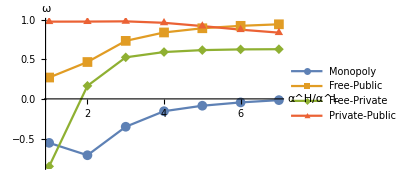

degreeoftslope.png

```mathematica
middle=Grid[Transpose[Map[Flatten,Prepend[Take[-cft,All,{8,8}],{{"sw","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}]]]];
ListLinePlot[middle[[1,2;;8,2;;8]],DataRange->{1,7},AxesLabel->{"Heterogeneity","Social Welfare"},PlotLegends->{"Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{Heterogeneity,ω},Axes->{True,True},ImageSize->500];
somedayft=Take[Map[Flatten,Prepend[Take[-cft,All,{8,8}],{{"sw","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}]],{2,8},{2,8}];
gooddayft=Map[(#-#[[2]])/(#[[3]]-#[[2]])&,somedayft];
nicedayft=ListLinePlot[Transpose[gooddayft[[All,4;;7]]],DataRange->{1,7},PlotLegends->{"Monopoly","Free-Public","Free-Private","Private-Public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{"α^H/α^L",ω},Axes->{True,True},ImageSize->300]
Export["degreeoftslope.png",nicedayft]
```

sw | price h | price h | price h | price h | price h | price h | price h
Stackelberg-private | 20.3288 | 26.2276 | 27.0179 | 27.4696 | 27.7648 | 27.9737 | 28.1298
free-free | 10.9128 | 14.0307 | 15.5076 | 16.3692 | 16.9336 | 17.3321 | 17.6283
public-public | 16.9681 | 18.5543 | 18.5743 | 19.4773 | 20.1019 | 20.5417 | 20.8682
Monopoly | 24.5164 | 26.7077 | 27.2839 | 27.5963 | 28.0142 | 28.3317 | 28.5746
free-public | 12.5424 | 14.5526 | 18.5204 | 19.4773 | 20.1019 | 20.5417 | 20.8682
free-private | 15.8657 | 20.7205 | 23.2728 | 25.014 | 26.2089 | 27.0814 | 27.747
private-public | 17.8169 | 19.4395 | 19.4898 | 19.667 | 20.1019 | 20.5417 | 20.8682

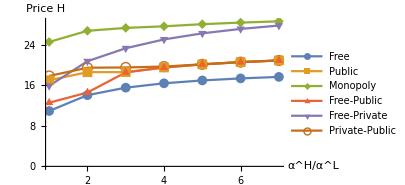

degreeoftslopeph.png

```mathematica
middleph=Grid[Transpose[Map[Flatten,Prepend[Take[cft,All,{11,11}],{{"ph","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}]]]]
nicedayftph=ListLinePlot[middleph[[1,3;;8,2;;8]],DataRange->{1,7},PlotLegends->{"Free","Public","Monopoly","Free-Public","Free-Private","Private-Public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{"α^H/α^L","Price H"},Axes->{True,True},ImageSize->300]
Export["degreeoftslopeph.png",nicedayftph]
```

sw | price l | price l | price l | price l | price l | price l | price l
Stackelberg-private | 20.3288 | 21.6274 | 19.4625 | 18.172 | 17.3133 | 16.7002 | 16.2402
free-free | 10.9128 | 7.01536 | 5.16921 | 4.0923 | 3.38673 | 2.88868 | 2.51834
public-public | 16.9681 | 13.6844 | 12.3674 | 10.355 | 8.89657 | 7.80724 | 6.96022
Monopoly | 24.5164 | 21.6274 | 19.6516 | 18.3788 | 17.5624 | 16.9717 | 16.5228
free-public | 12.5424 | 9.21926 | 7.75761 | 6.25351 | 5.24179 | 4.51356 | 3.96386
free-private | 15.8657 | 10.3602 | 7.75761 | 6.25351 | 5.24179 | 4.51356 | 3.96386
private-public | 17.8169 | 14.672 | 13.4647 | 12.4167 | 12.0611 | 11.9827 | 11.9247

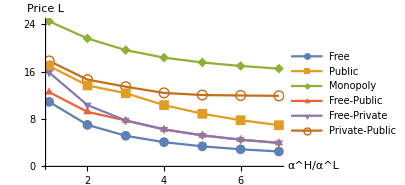

degreeoftslopepl.png

```mathematica
middlepl=Grid[Transpose[Map[Flatten,Prepend[Take[cft,All,{12,12}],{{"pl","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}]]]]
nicedayftpl=ListLinePlot[middlepl[[1,3;;8,2;;8]],DataRange->{1,7},PlotLegends->{"Free","Public","Monopoly","Free-Public","Free-Private","Private-Public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{"α^H/α^L","Price L"},Axes->{True,True},ImageSize->300]
Export["degreeoftslopepl.png",nicedayftpl]
```

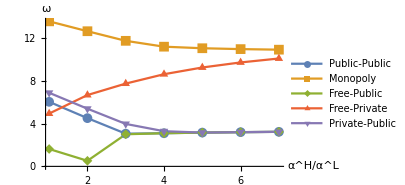

degreeoftslopephd.png

```mathematica
somedayftphd=Take[Map[Flatten,Prepend[Take[cft,All,{11,11}],{{"sw","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}]],{2,8},{2,8}];
gooddayftphd=Map[#-#[[2]]&,somedayftphd];
nicedayftphd=ListLinePlot[Transpose[gooddayftphd[[All,3;;7]]],DataRange->{1,7},PlotLegends->{"Public-Public","Monopoly","Free-Public","Free-Private","Private-Public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{"α^H/α^L",ω},Axes->{True,True},ImageSize->300]
Export["degreeoftslopephd.png",nicedayftphd]
(*monopoly is bad for both high and low types, free is good for the low types and public is good for the high types. *)
```

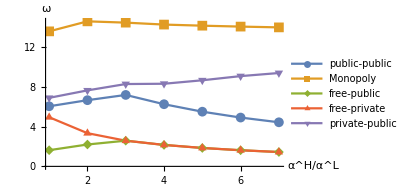

degreeoftslopepld.png

```mathematica
somedayftpld=Take[Map[Flatten,Prepend[Take[cft,All,{12,12}],{{"sw","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}]],{2,8},{2,8}];
gooddayftpld=Map[#-#[[2]]&,somedayftpld];
nicedayftpld=ListLinePlot[Transpose[gooddayftpld[[All,3;;7]]],DataRange->{1,7},PlotLegends->{"public-public","Monopoly","free-public","free-private","private-public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{"α^H/α^L",ω},Axes->{True,True},ImageSize->300]
Export["degreeoftslopepld.png",nicedayftpld]
```

sw | nh1 | nh1 | nh1 | nh1 | nh1 | nh1 | nh1
Stackelberg-private | 7250.97 | 0. | 0. | 0. | 0. | 0. | 0.
free-free | 9000. | 9000. | 9000. | 9000. | 9000. | 9000. | 9000.
public-public | 6996.96 | 0. | 0. | 0. | 0. | 0. | 0.
Monopoly | 4500. | 0. | 0. | 0. | 122.591 | 204.082 | 258.488
free-public | 10344. | 0. | 0. | 0. | 0. | 0. | 0.
free-private | 8988.8 | 220.989 | 0. | 0. | 0. | 0. | 0.
private-public | 6355.02 | 0. | 0. | 0. | 0. | 0. | 0.

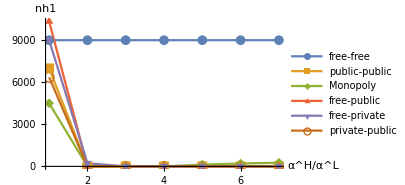

sw | nh2 | nh2 | nh2 | nh2 | nh2 | nh2 | nh2
Stackelberg-private | 837.492 | 6933.25 | 7218.48 | 7388.74 | 7500.59 | 7579.29 | 7637.52
free-free | 3000. | 3000. | 3000. | 3000. | 3000. | 3000. | 3000.
public-public | 2487.59 | 10120.8 | 10726.1 | 10708.9 | 10683.9 | 10666.7 | 10654.1
Monopoly | 1848.84 | 6733.81 | 7107.99 | 7336.1 | 7274.39 | 7226.51 | 7194.3
free-public | 979.029 | 11783.2 | 10748.5 | 10708.9 | 10683.9 | 10666.7 | 10654.1
free-private | 953.677 | 9000. | 8774.23 | 8408.8 | 8146.9 | 7950. | 7796.57
private-public | 2776.92 | 9753.13 | 10345.7 | 10630.1 | 10683.9 | 10666.7 | 10654.1

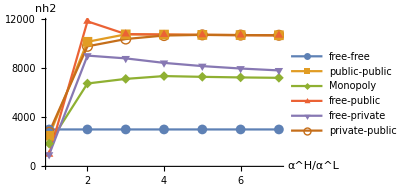

sw | nl1 | nl1 | nl1 | nl1 | nl1 | nl1 | nl1
Stackelberg-private | 0. | 6569.34 | 6753.29 | 6876.53 | 6964.85 | 7031.25 | 7082.99
free-free | 0. | 0. | 0. | 0. | 0. | 0. | 0.
public-public | 0. | 8777.83 | 10766.3 | 11386.6 | 11821. | 12162.2 | 12437.2
Monopoly | 0. | 6569.34 | 6644.16 | 6757.17 | 6821.14 | 6874.57 | 6919.89
free-public | 0. | 11827.4 | 13506.6 | 13753.1 | 13929.7 | 14062.5 | 14166.
free-private | 4096. | 13070.1 | 13506.6 | 13753.1 | 13929.7 | 14062.5 | 14166.
private-public | 0. | 8103.27 | 10069.3 | 10197.1 | 9995.18 | 9753.09 | 9572.85

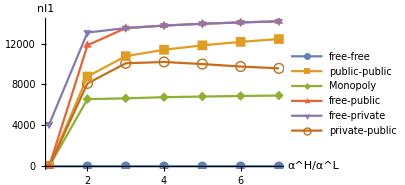

sw | nl2 | nl2 | nl2 | nl2 | nl2 | nl2 | nl2
Stackelberg-private | 9567.31 | 0. | 0. | 0. | 0. | 0. | 0.
free-free | 15000. | 15000. | 15000. | 15000. | 15000. | 15000. | 15000.
public-public | 11506.3 | 2374.39 | 80.537 | 0. | 0. | 0. | 0.
Monopoly | 7151.16 | 0. | 0. | 0. | 0. | 0. | 0.
free-public | 14059.8 | 1901.05 | 0. | 0. | 0. | 0. | 0.
free-private | 8046.32 | 0. | 0. | 0. | 0. | 0. | 0.
private-public | 11016.6 | 2479.09 | 144.549 | 0. | 0. | 0. | 0.

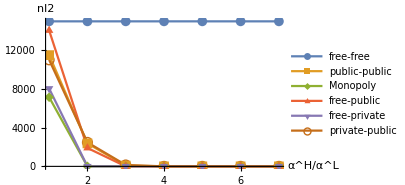

```mathematica
www=Grid[Transpose[Map[Flatten,Prepend[Take[cft,All,{2,2}],{{"sw","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}]]]]
wwx=ListLinePlot[www[[1,3;;8,2;;8]],DataRange->{1,7},PlotLegends->{"free-free","public-public","Monopoly","free-public","free-private","private-public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{"α^H/α^L","nh1"},Axes->{True,True},ImageSize->300]
www=Grid[Transpose[Map[Flatten,Prepend[Take[cft,All,{3,3}],{{"sw","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}]]]]
wwx=ListLinePlot[www[[1,3;;8,2;;8]],DataRange->{1,7},PlotLegends->{"free-free","public-public","Monopoly","free-public","free-private","private-public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{"α^H/α^L","nh2"},Axes->{True,True},ImageSize->300]
www=Grid[Transpose[Map[Flatten,Prepend[Take[cft,All,{4,4}],{{"sw","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}]]]]
wwx=ListLinePlot[www[[1,3;;8,2;;8]],DataRange->{1,7},PlotLegends->{"free-free","public-public","Monopoly","free-public","free-private","private-public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{"α^H/α^L","nl1"},Axes->{True,True},ImageSize->300]
www=Grid[Transpose[Map[Flatten,Prepend[Take[cft,All,{5,5}],{{"sw","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}]]]]
wwx=ListLinePlot[www[[1,3;;8,2;;8]],DataRange->{1,7},PlotLegends->{"free-free","public-public","Monopoly","free-public","free-private","private-public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{"α^H/α^L","nl2"},Axes->{True,True},ImageSize->300]
```

## Bertrand Competition and queue-eliminating tolls

```mathematica
degreeqet[dgr_]:=Module[{ah,bh,al,bl,h,l,alpha,beta,gamma,nh1,nh2,nl1,nl2,m,pi1,pi2,sw,eh,el,c,ph,pl,csh,csl,tau1,tau2,tau1n,tau2n,idc,rqprpu,rqprpr,rqzz,rqo,rqm,rqzpr,rqzpu,rqstbp,rqstb,min,max,ss,a,list,mtrxqt,pi,n},
alpha=(90*dgr)/(4+5 dgr);
beta=39/64*alpha;(*marginal schedule delay cost of arriving early*)
gamma=1521/10/64*alpha;(*marginal schedule delay cost of arriving late*)
h=beta*gamma/(beta+gamma)/s1; (*marginal congestion cost for high type*)
l=h/dgr;(*marginal congestion cost for low type,9/10*h*)
(*The slopes of the demand curve does not change, only the intercept changes*)
bh=41067/17059840;
bl=369603/213248000;
ah=bh*nh+h*(nh+nl)*sa;(*because h and l changes, to keep nh and nl unchanged, ah and al must also change. So ah increases but al decreases*)
al=bl*nl+l*(nh+nl)*sa;
ft[tau1_,tau2_]:=(*ft calculates the equilibrium given flat tolls*)
Module[{nh1,nh2,nl1,nl2,m,pi1,pi2,sw,eh,el,c,ph,pl,csh,csl},
pi1=-tau1*(nh1+nl1);
pi2=-tau2*(nh2+nl2);
sw=-ah*(nh1+nh2)+bh*(nh1+nh2)^2/2-al*(nl1+nl2)+bl*(nl1+nl2)^2/2+h*(nh1+nl1)*nh1+l*(nh1+nl1)*nl1+h*g*(nh2+nl2)*nh2+l*g*(nh2+nl2)*nl2;
csh=ah*(nh1+nh2)-bh*(nh1+nh2)^2/2-(h*nh1+h*nl1+tau1)*nh1-(h*g*nh2+h*g*nl2+tau2)*nh2;
csl=al*(nl1+nl2)-bl*(nl1+nl2)^2/2-(l*nh1+l*nl1+tau1)*nl1-(l*g*nh2+l*g*nl2+tau2)*nl2;
c=(h*nh1+h*nl1)*nh1+(l*nh1+l*nl1)*nl1+(h*g*nh2+h*g*nl2)*nh2+(l*g*nh2+l*g*nl2)*nl2;
ph=ah-bh*(nh1+nh2);
pl=al-bl*(nl1+nl2);
m=Minimize[0,
{nh1*(ah-bh*(nh1+nh2)-h*nh1-h*nl1-tau1)==0,nh2*(ah-bh*(nh1+nh2)-h*g*nh2-h*g*nl2-tau2)==0,nl1*(al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1)==0,nl2*(al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2)==0,ah-bh*(nh1+nh2)-h*nh1-h*nl1-tau1≤0,ah-bh*(nh1+nh2)-h*g*nh2-h*g*nl2-tau2≤0,al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1≤0,al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2≤0,
nh1≥0,nh2≥0,nl1≥0,nl2>=0},
{nh1,nh2,nl1,nl2}][[2]];
eh=(ah-bh*(nh1+nh2))/((nh1+nh2)*(-bh));
el=(al-bl*(nl1+nl2))/((nl1+nl2)*(-bl));
{nh1,nh2,nl1,nl2,pi1,pi2,sw,tau1,tau2,ph,pl,csh,csl}/.m
];
qetb[tau1_,tau2_]:=(*qet is the function to calculate the equilibrium given that both parties use queue-eliminating tolls.*)
Module[{nh1,nh2,nl1,nl2,m,pi1,pi2,sw,eh,el,c,ph,pl,csh,csl},
pi1=-(tau1+l*nl1+h*nh1/2)*nh1-(tau1+l*nl1/2)*nl1;
pi2=-(tau2+l*g*nl2+h*g*nh2/2)*nh2-(tau2+l*g*nl2/2)*nl2;
sw=-ah*(nh1+nh2)+bh*(nh1+nh2)^2/2-al*(nl1+nl2)+bl*(nl1+nl2)^2/2+h*nh1/2*nh1+(l*nh1+l*nl1/2)*nl1+h*g*nh2/2*nh2+(l*g*nh2+l*g*nl2/2)*nl2;
csh=ah*(nh1+nh2)-bh*(nh1+nh2)^2/2-(tau1+l*nl1+h*nh1)*nh1-(tau2+l*g*nl2+h*g*nh2)*nh2;
csl=al*(nl1+nl2)-bl*(nl1+nl2)^2/2-(tau1+l*nh1+l*nl1)*nl1-(tau2+l*g*nh2+l*g*nl2)*nl2;
c=h*nh1/2*nh1+(l*nh1+l*nl1/2)*nl1+h*g*nh2/2*nh2+(l*g*nh2+l*g*nl2/2)*nl2;
ph=ah-bh*(nh1+nh2);
pl=al-bl*(nl1+nl2);
m=Minimize[0,
{nh1*(ah-bh*(nh1+nh2)-h*nh1-l*nl1-tau1)==0,nh2*(ah-bh*(nh1+nh2)-h*g*nh2-l*g*nl2-tau2)==0,nl1*(al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1)==0,nl2*(al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2)==0,ah-bh*(nh1+nh2)-h*nh1-l*nl1-tau1≤0,ah-bh*(nh1+nh2)-h*g*nh2-l*g*nl2-tau2≤0,al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1≤0,al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2≤0,
nh1>=0,nh2>=0,nl1≥0,nl2≥0},{nh1,nh2,nl1,nl2}][[2]];
eh=(ah-bh*(nh1+nh2))/((nh1+nh2)*(-bh));
el=(al-bl*(nl1+nl2))/((nl1+nl2)*(-bl));
{nh1,nh2,nl1,nl2,pi1,pi2,sw,tau1,tau2,ph,pl,csh,csl}/.m
];
qets[tau1_,tau2_]:=(*qets calculates the equilibrium, when link 1 uses flat toll but link 2 uses the queue-eliminating toll.*)
Module[{nh1,nh2,nl1,nl2,m,pi1,pi2,sw,eh,el,c,ph,pl,csh,csl},
pi1=-tau1*(nh1+nl1);
pi2=-(tau2+l*g*nl2+h*g*nh2/2)*nh2-(tau2+l*g*nl2/2)*nl2;
sw=-ah*(nh1+nh2)+bh*(nh1+nh2)^2/2-al*(nl1+nl2)+bl*(nl1+nl2)^2/2+(h*nh1+h*nl1)*nh1+(l*nh1+l*nl1)*nl1+h*g*nh2/2*nh2+(l*g*nh2+l*g*nl2/2)*nl2;
csh=ah*(nh1+nh2)-bh*(nh1+nh2)^2/2-(tau1+h*nl1+h*nh1)*nh1-(tau2+l*g*nl2+h*g*nh2)*nh2;
csl=al*(nl1+nl2)-bl*(nl1+nl2)^2/2-(tau1+l*nh1+l*nl1)*nl1-(tau2+l*g*nh2+l*g*nl2)*nl2;
c=(h*nh1+h*nl1)*nh1+(l*nh1+l*nl1)*nl1+h*g*nh2/2*nh2+(l*g*nh2+l*g*nl2/2)*nl2;
ph=ah-bh*(nh1+nh2);
pl=al-bl*(nl1+nl2);
m=Minimize[0,
{nh1*(ah-bh*(nh1+nh2)-h*nh1-h*nl1-tau1)==0,nh2*(ah-bh*(nh1+nh2)-h*g*nh2-l*g*nl2-tau2)==0,nl1*(al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1)==0,nl2*(al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2)==0,ah-bh*(nh1+nh2)-h*nh1-h*nl1-tau1≤0,ah-bh*(nh1+nh2)-h*g*nh2-l*g*nl2-tau2≤0,al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1≤0,al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2≤0,
nh1>=0,nh2>=0,nl1≥0,nl2≥0},{nh1,nh2,nl1,nl2}][[2]];
eh=(ah-bh*(nh1+nh2))/((nh1+nh2)*(-bh));
el=(al-bl*(nl1+nl2))/((nl1+nl2)*(-bl));
{nh1,nh2,nl1,nl2,pi1,pi2,sw,tau1,tau2,ph,pl,csh,csl}/.m
];
qetb1[tau2_]:=(*qet1 calculates best response of private supplier on link 1, given both use queue-eliminating tolls*)
Module[{nh1,nh2,nl1,nl2,m,tau1},
m=Minimize[-(tau1+l*nl1+h*nh1/2)*nh1-(tau1+l*nl1/2)*nl1,
{nh1*(ah-bh*(nh1+nh2)-h*nh1-l*nl1-tau1)==0,nh2*(ah-bh*(nh1+nh2)-h*g*nh2-l*g*nl2-tau2)==0,nl1*(al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1)==0,nl2*(al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2)==0,
ah-bh*(nh1+nh2)-h*nh1-l*nl1-tau1≤0,
ah-bh*(nh1+nh2)-h*g*nh2-l*g*nl2-tau2≤0,
al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1≤0,
al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2≤0,
nh1>=0,nh2>=0,nl1≥0,nl2≥0},{nh1,nh2,nl1,nl2,tau1}][[2]];
{tau1}/.m
];
qetb2[tau1_]:=(*qet2 calculates best response of private supplier on link 2, given both use queue-eliminating tolls*)
Module[{nh1,nh2,nl1,nl2,m,tau2},
m=Minimize[-(tau2+l*g*nl2+h*g*nh2/2)*nh2-(tau2+l*g*nl2/2)*nl2,
{nh1*(ah-bh*(nh1+nh2)-h*nh1-l*nl1-tau1)==0,nh2*(ah-bh*(nh1+nh2)-h*g*nh2-l*g*nl2-tau2)==0,nl1*(al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1)==0,nl2*(al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2)==0,
ah-bh*(nh1+nh2)-h*nh1-l*nl1-tau1≤0,
ah-bh*(nh1+nh2)-h*g*nh2-l*g*nl2-tau2≤0,
al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1≤0,
al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2≤0,
nh1>=0,nh2>=0,nl1≥0,nl2≥0},{nh1,nh2,nl1,nl2,tau2}][[2]];
{tau2}/.m
];
qetbp1[tau2_]:=(*qetp1 calculates best response for social planner on link 1 when both use queue-eliminating tolls. *)
Module[{nh1,nh2,nl1,nl2,m,tau1},
m=Minimize[-ah*(nh1+nh2)+bh*(nh1+nh2)^2/2-al*(nl1+nl2)+bl*(nl1+nl2)^2/2+h*nh1^2/2+(l*nh1+l*nl1/2)*nl1+h*g*nh2^2/2+(l*g*nh2+l*g*nl2/2)*nl2,
{nh1*(ah-bh*(nh1+nh2)-h*nh1-l*nl1-tau1)==0,nh2*(ah-bh*(nh1+nh2)-h*g*nh2-l*g*nl2-tau2)==0,nl1*(al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1)==0,nl2*(al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2)==0,
ah-bh*(nh1+nh2)-h*nh1-l*nl1-tau1≤0,
ah-bh*(nh1+nh2)-h*g*nh2-l*g*nl2-tau2≤0,
al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1≤0,
al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2≤0,
nh1>=0,nh2>=0,nl1≥0,nl2≥0},{nh1,nh2,nl1,nl2,tau1}][[2]];
{tau1}/.m
];
qetbp2[tau1_]:=(*qetp2 calculates best response for social planner on link 2 when both use queue-eliminating tolls. *)
Module[{nh1,nh2,nl1,nl2,m,tau2},
m=Minimize[-ah*(nh1+nh2)+bh*(nh1+nh2)^2/2-al*(nl1+nl2)+bl*(nl1+nl2)^2/2+h*nh1^2/2+(l*nh1+l*nl1/2)*nl1+h*g*nh2^2/2+(l*g*nh2+l*g*nl2/2)*nl2,
{nh1*(ah-bh*(nh1+nh2)-h*nh1-l*nl1-tau1)==0,nh2*(ah-bh*(nh1+nh2)-h*g*nh2-l*g*nl2-tau2)==0,nl1*(al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1)==0,nl2*(al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2)==0,
ah-bh*(nh1+nh2)-h*nh1-l*nl1-tau1≤0,
ah-bh*(nh1+nh2)-h*g*nh2-l*g*nl2-tau2≤0,
al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1≤0,
al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2≤0,
nh1>=0,nh2>=0,nl1≥0,nl2≥0},{nh1,nh2,nl1,nl2,tau2}][[2]];
{tau2}/.m
];
qets2[tau1_]:=(*qetp2s calculates the best response for private supplier on link 2, given link 1 uses flat toll but link 2 uses queue-eliminating tolls*)
Module[{nh1,nh2,nl1,nl2,m,tau2},
m=Minimize[-(tau2+l*g*nl2+h*g*nh2/2)*nh2-(tau2+l*g*nl2/2)*nl2,
{nh1*(ah-bh*(nh1+nh2)-h*nh1-h*nl1-tau1)==0,nh2*(ah-bh*(nh1+nh2)-h*g*nh2-l*g*nl2-tau2)==0,nl1*(al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1)==0,nl2*(al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2)==0,
ah-bh*(nh1+nh2)-h*nh1-h*nl1-tau1≤0,
ah-bh*(nh1+nh2)-h*g*nh2-l*g*nl2-tau2≤0,
al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1≤0,
al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2≤0,
nh1>=0,nh2>=0,nl1≥0,nl2≥0},{nh1,nh2,nl1,nl2,tau2}][[2]];
{tau2}/.m
];
qetsp2[tau1_]:=(*qetp2s calculates the best response for social planner on link 2, given link 1 uses flat toll but link 2 uses queue-eliminating tolls*)
Module[{nh1,nh2,nl1,nl2,m,tau2},
m=Minimize[-ah*(nh1+nh2)+bh*(nh1+nh2)^2/2-al*(nl1+nl2)+bl*(nl1+nl2)^2/2+(h*nh1+h*nl1)*nh1+(l*nh1+l*nl1)*nl1+h*g*nh2^2/2+(l*g*nh2+l*g*nl2/2)*nl2,
{nh1*(ah-bh*(nh1+nh2)-h*nh1-h*nl1-tau1)==0,nh2*(ah-bh*(nh1+nh2)-h*g*nh2-l*g*nl2-tau2)==0,nl1*(al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1)==0,nl2*(al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2)==0,
ah-bh*(nh1+nh2)-h*nh1-h*nl1-tau1≤0,
ah-bh*(nh1+nh2)-h*g*nh2-l*g*nl2-tau2≤0,
al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1≤0,
al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2≤0,
nh1>=0,nh2>=0,nl1≥0,nl2≥0},{nh1,nh2,nl1,nl2,tau2}][[2]];
{tau2}/.m
];
(*Private-Public*)
tau1=0;
tau2=0;
tau1n=tau1;
tau2n=tau2;
idc=1;
While[idc>10^-5,
tau1n=qetb1[tau2n][[1]];
tau2n=qetbp2[tau1n][[1]];
idc=Max[Abs[tau2n-tau2],Abs[tau1n-tau1]];
tau1=tau1n;
tau2=tau2n;
Print[N[qetb[tau1,tau2]],N[idc]];
];
rqprpu=qetb[tau1,tau2];
Print["private-public:", N[rqprpu]];
(*Private-Private
tau1=0;
tau2=0;
tau1n=tau1;
tau2n=tau2;
idc=1;
While[idc>10^-5,
tau1n=qetb1[tau2n][[1]];
tau2n=qetb2[tau1n][[1]];
idc=Max[Abs[tau2n-tau2],Abs[tau1n-tau1]];
tau1=tau1n;
tau2=tau2n;
Print[N[qetb[tau1,tau2]],N[idc]];
];
rqprpr=qetb[tau1,tau2];
Print["private-private:", N[rqprpr]];*)
(*free-free*)
tau1=0;tau2=0;
rqzz=ft[tau1,tau2];
Print["free-free:", N[rqzz]];
(*public-public*)
Clear[tau1,tau2];
sw=-ah*(nh1+nh2)+bh*(nh1+nh2)^2/2-al*(nl1+nl2)+bl*(nl1+nl2)^2/2+h*nh1^2/2+(l*nh1+l*nl1/2)*nl1+h*g*nh2^2/2+(l*g*nh2+l*g*nl2/2)*nl2;
m=Minimize[sw,
{nh1*(ah-bh*(nh1+nh2)-h*nh1-l*nl1-tau1)==0,nh2*(ah-bh*(nh1+nh2)-h*g*nh2-l*g*nl2-tau2)==0,nl1*(al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1)==0,nl2*(al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2)==0,
ah-bh*(nh1+nh2)-h*nh1-l*nl1-tau1≤0,
ah-bh*(nh1+nh2)-h*g*nh2-l*g*nl2-tau2≤0,
al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1≤0,
al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2≤0,
nh1>=0,nh2>=0,nl1≥0,nl2≥0},{nh1,nh2,nl1,nl2,tau1,tau2}][[2]];
tau1=tau1/.m;
tau2=tau2/.m;
rqo=qetb[tau1,tau2];
Print["public-public:", N[rqo]];
(*Monopoly*)
Clear[tau1,tau2];
pi=-(tau1+l*nl1+h*nh1/2)*nh1-(tau1+l*nl1/2)*nl1-(tau2+l*g*nl2+h*g*nh2/2)*nh2-(tau2+l*g*nl2/2)*nl2;
m=Minimize[pi,
{nh1*(ah-bh*(nh1+nh2)-h*nh1-l*nl1-tau1)==0,nh2*(ah-bh*(nh1+nh2)-h*g*nh2-l*g*nl2-tau2)==0,nl1*(al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1)==0,nl2*(al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2)==0,
ah-bh*(nh1+nh2)-h*nh1-l*nl1-tau1≤0,
ah-bh*(nh1+nh2)-h*g*nh2-l*g*nl2-tau2≤0,
al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1≤0,
al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2≤0,
nh1>=0,nh2>=0,nl1≥0,nl2≥0},{nh1,nh2,nl1,nl2,tau1,tau2}][[2]];
tau1=tau1/.m;
tau2=tau2/.m;
rqm=qetb[tau1,tau2];
Print["Monopoly:", N[rqm]];
(*free-Public*)
tau1=0;
tau2=qetsp2[tau1][[1]];
rqzpu=qets[tau1,tau2];
Print["free-Public:", N[rqzpu]];
(*free-Private*)
tau1=0;
tau2=qets2[tau1][[1]];
rqzpr=qets[tau1,tau2];
Print["free-private:", N[rqzpr]];
(*Stackelberg Public
idc=1;
ss=5;
min=0;
max=15;
While[idc>10^-6,
list=ParallelTable[qetb[qetb1[tau2][[1]],tau2][[7]],{tau2,min,max,(max-min)/ss}];
a=Position[list,Min[list]][[1]][[1]];
min=min+(max-min)*(a-2)/ss;
max=min+(max-min)*a/ss;
idc=max-min;
(*Print[a];*)
];
tau2=min;
rqstb=qetb[qetb1[tau2][[1]],tau2];
Print["Stackelberg Public:", N[rqstb]];*)
(*Stackelberg Private*)
idc=1;
ss=5;
min=0;
max=Max[ah,al];
While[idc>10^-6,
list=ParallelTable[qetb[qetb1[tau2][[1]],tau2][[6]],{tau2,min,max,(max-min)/ss}];
a=Position[list,Min[list]][[1]][[1]];
min=min+(max-min)*(a-2)/ss;
max=min+(max-min)*a/ss;
idc=max-min;
(*Print[a];*)
];
tau2=min;
rqstbp=qetb[qetb1[tau2][[1]],tau2];
Print["Stackelberg Private:", N[rqstbp]];
mtrxqt=MapThread[Prepend,{Prepend[Transpose[N[{rqstbp,rqzz,rqo,rqm,rqzpu,rqzpr,rqprpu},6]],{"Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}],{dgr "QE toll","nh1","nh2","nl1","nl2","pi1","pi2","sw","tau1","tau2","price h","price l","cs h","cs l"}}]
]
```

```mathematica
cqt=ParallelMap[degreeqet,{1,2,3,4,5,6,7}];
Export["degreeqetslope.xls",cqt,"XLS"]
```

{7760.47,3720.66,0.,14279.3,-57869.2,-120698.,-513924.,2.75201,1.24905,12.1618,12.1618,158656.,176700.}2.75201

{4523.47,9046.94,4097.23,10117.,-46713.3,-95933.,-539391.,1.57978,1.02768,11.7273,6.53114,221653.,175092.}1.57978

{4735.05,9470.1,4282.67,10076.1,-42136.,-85726.2,-549407.,1.10468,0.820424,11.6253,4.49807,242873.,178672.}1.10468

{4839.85,9679.69,4411.19,10058.4,-39491.6,-79925.8,-554600.,0.849077,0.676147,11.5632,3.43765,253743.,181440.}0.849077

{7692.97,3759.9,0.,14240.1,-58204.,-121922.,-513733.,2.90189,1.31707,12.2299,12.2299,157876.,175730.}0.149877

{4721.25,9442.49,4185.56,10103.7,-42985.8,-87884.3,-549276.,1.26688,0.940887,11.725,4.61854,241459.,176946.}0.1622

{4827.16,9654.32,4320.67,10083.8,-40332.4,-81948.6,-554505.,0.990864,0.789057,11.6548,3.55056,252414.,179810.}0.141788

{4509.45,9018.9,4001.5,10145.,-47462.3,-98036.1,-539208.,1.76015,1.14501,11.8285,6.64848,220281.,173428.}0.180368

{7689.29,3762.04,0.,14238.,-58221.8,-121989.,-513722.,2.91005,1.32077,12.2336,12.2336,157834.,175677.}0.00816238

{4825.04,9650.09,4305.55,10088.,-40470.3,-82286.4,-554488.,1.01454,0.807912,11.6701,3.56942,252193.,179538.}0.0236772

{4507.85,9015.7,3990.57,10148.2,-47545.8,-98276.3,-539186.,1.78074,1.15841,11.8401,6.66187,220125.,173239.}0.0205931

{4719.22,9438.44,4171.3,10107.8,-43108.,-88201.2,-549255.,1.2907,0.958575,11.7397,4.63623,241252.,176694.}0.0238158

{7689.09,3762.16,0.,14237.8,-58222.8,-121993.,-513721.,2.9105,1.32098,12.2338,12.2338,157831.,175675.}0.000444529

{7689.08,3762.16,0.,14237.8,-58222.8,-121993.,-513721.,2.91052,1.32099,12.2338,12.2338,157831.,175674.}0.0000242093

{4507.67,9015.33,3989.32,10148.6,-47555.3,-98303.7,-539183.,1.78309,1.15993,11.8414,6.6634,220107.,173217.}0.00235118

{4824.69,9649.38,4303.03,10088.7,-40493.3,-82342.8,-554485.,1.0185,0.811061,11.6727,3.57257,252156.,179493.}0.00395386

{4718.92,9437.84,4169.21,10108.4,-43125.9,-88247.8,-549252.,1.29419,0.961172,11.7418,4.63882,241222.,176657.}0.00349687

{7689.08,3762.16,0.,14237.8,-58222.8,-121993.,-513721.,2.91052,1.32099,12.2338,12.2338,157831.,175674.}1.31846×10^-6

private-public:{7689.08,3762.16,0.,14237.8,-58222.8,-121993.,-513721.,2.91052,1.32099,12.2338,12.2338,157831.,175674.}

free-free:{9000.,3000.,0.,15000.,0.,0.,-368307.,0.,0.,10.9128,10.9128,173321.,194986.}

{4718.88,9437.76,4168.9,10108.5,-43128.5,-88254.6,-549251.,1.29471,0.961553,11.7421,4.6392,241217.,176651.}0.000513445

{4507.65,9015.29,3989.18,10148.6,-47556.4,-98306.8,-539183.,1.78336,1.16011,11.8416,6.66358,220105.,173215.}0.00026844

{4824.63,9649.26,4302.61,10088.8,-40497.1,-82352.2,-554484.,1.01916,0.811586,11.6731,3.57309,252150.,179485.}0.000660256

public-public:{9000.,3000.,0.,15000.,-49107.5,-98215.1,-515629.,0.,0.,10.9128,10.9128,173321.,194986.}

Monopoly:{5251.71,2041.14,0.,8462.29,-100098.,-200196.,-426367.,15.8761,15.8761,22.244,22.244,64015.1,62057.8}

free-Public:{7401.57,5403.56,0.,16118.2,0.,-52743.,-475243.,0.,-4.07329,8.97464,8.97464,197359.,225142.}

{4718.87,9437.74,4168.86,10108.5,-43128.9,-88255.6,-549251.,1.29478,0.961609,11.7422,4.63926,241216.,176650.}0.0000753891

{4507.64,9015.29,3989.16,10148.6,-47556.5,-98307.2,-539183.,1.78339,1.16013,11.8416,6.6636,220105.,173214.}0.0000306486

{4824.62,9649.24,4302.54,10088.9,-40497.7,-82353.8,-554484.,1.01927,0.811674,11.6732,3.57318,252149.,179484.}0.000110256

free-private:{10610.,63.3138,1024.,12133.3,0.,-126959.,-414095.,0.,6.71214,14.1065,14.1065,137114.,150022.}

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

{4718.87,9437.74,4168.85,10108.5,-43129.,-88255.7,-549251.,1.29479,0.961617,11.7422,4.63927,241216.,176650.}0.0000110694

{4507.64,9015.29,3989.16,10148.6,-47556.5,-98307.2,-539183.,1.7834,1.16013,11.8416,6.6636,220105.,173214.}3.49924×10^-6

{4824.62,9649.24,4302.53,10088.9,-40497.8,-82354.1,-554484.,1.01928,0.811689,11.6732,3.5732,252149.,179484.}0.0000184118

private-public:{4507.64,9015.29,3989.16,10148.6,-47556.5,-98307.2,-539183.,1.7834,1.16013,11.8416,6.6636,220105.,173214.}

free-free:{9000.,3000.,0.,15000.,0.,0.,-368307.,0.,0.,15.5076,5.16921,173321.,194986.}

public-public:{4646.24,9292.49,4935.72,9871.43,-38766.,-77532.,-540151.,0.,0.,10.8407,5.50347,233848.,190004.}

{4718.87,9437.74,4168.85,10108.5,-43129.,-88255.8,-549251.,1.29479,0.961619,11.7422,4.63927,241216.,176650.}1.62532×10^-6

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

Monopoly:{3034.58,6069.16,2341.24,4682.48,-99096.8,-198194.,-439796.,15.9061,15.9061,22.4796,18.9938,99753.4,42751.9}

{4824.62,9649.24,4302.52,10088.9,-40497.9,-82354.1,-554484.,1.01929,0.811691,11.6732,3.5732,252149.,179484.}3.07459×10^-6

free-Public:{0.,13580.2,6796.87,8933.21,0.,-68071.9,-504474.,0.,-2.56154,11.7037,3.90383,221973.,214428.}

private-public:{4718.87,9437.74,4168.85,10108.5,-43129.,-88255.8,-549251.,1.29479,0.961619,11.7422,4.63927,241216.,176650.}

free-free:{9000.,3000.,0.,15000.,0.,0.,-368307.,0.,0.,16.9336,3.38673,173321.,194986.}

free-private:{0.,8774.23,13506.6,0.,0.,-171038.,-421793.,0.,15.7135,23.2728,7.75761,92663.,158093.}

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

private-public:{4824.62,9649.24,4302.52,10088.9,-40497.9,-82354.1,-554484.,1.01929,0.811691,11.6732,3.5732,252149.,179484.}

free-free:{9000.,3000.,0.,15000.,0.,0.,-368307.,0.,0.,17.6283,2.51834,173321.,194986.}

public-public:{4829.06,9658.12,4944.05,9888.1,-35521.7,-71043.4,-549825.,0.,0.,10.9464,3.67765,252613.,190646.}

public-public:{4915.81,9831.63,4953.23,9906.47,-33912.1,-67824.2,-554863.,0.,0.,11.0146,2.76151,261771.,191355.}

Monopoly:{3201.68,6403.35,2212.69,4425.38,-99006.2,-198012.,-446246.,15.8422,15.8422,22.6989,17.8797,111041.,38186.}

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable :: subpar will be suppressed during this calculation.

free-Public:{5033.43,10066.9,0.,15861.2,0.,-24001.7,-516467.,0.,-2.98431,9.47048,1.8941,274448.,218018.}

Monopoly:{3279.95,6559.91,2153.01,4306.01,-99008.9,-198018.,-449718.,15.8014,15.8014,22.8283,17.3216,116538.,36153.8}

free-private:{0.,8146.9,13929.7,0.,0.,-182302.,-430341.,0.,18.5447,26.2089,5.24179,79886.5,168153.}

free-Public:{4976.46,10297.4,0.,15816.4,0.,-25613.8,-523195.,0.,-2.55021,9.74741,1.10331,280792.,216789.}

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

free-private:{0.,8028.41,14166.,0.,0.,-186721.,-438207.,0.,19.3262,27.1889,3.96386,77579.5,173906.}

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable :: subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable :: subpar will be suppressed during this calculation.

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable :: subpar will be suppressed during this calculation.

Stackelberg Private:{9750.76,337.81,0.,12345.2,-93631.5,-148003.,-496213.,3.69092,7.82473,15.514,15.514,122503.,132075.}

{4304.8,8609.59,3986.93,10171.4,-50691.2,-104860.,-530011.,2.01079,1.1543,11.8296,8.47407,200741.,173719.}2.01079

{4291.93,8583.85,3901.79,10197.2,-51290.9,-106708.,-529805.,2.19015,1.25726,11.9225,8.57703,199542.,172264.}0.179366

{4290.78,8581.56,3894.19,10199.5,-51343.1,-106873.,-529786.,2.20615,1.26645,11.9308,8.58622,199436.,172135.}0.0159997

{4290.68,8581.35,3893.52,10199.7,-51347.7,-106887.,-529784.,2.20758,1.26727,11.9316,8.58703,199426.,172123.}0.0014272

{4290.67,8581.33,3893.46,10199.7,-51348.1,-106889.,-529784.,2.20771,1.26734,11.9316,8.58711,199425.,172122.}0.000127309

{4290.67,8581.33,3893.45,10199.7,-51348.2,-106889.,-529784.,2.20772,1.26735,11.9316,8.58711,199425.,172122.}0.0000113561

{4290.67,8581.33,3893.45,10199.7,-51348.2,-106889.,-529784.,2.20772,1.26735,11.9316,8.58711,199425.,172122.}1.01299×10^-6

private-public:{4290.67,8581.33,3893.45,10199.7,-51348.2,-106889.,-529784.,2.20772,1.26735,11.9316,8.58711,199425.,172122.}

free-free:{9000.,3000.,0.,15000.,0.,0.,-368307.,0.,0.,14.0307,7.01536,173321.,194986.}

public-public:{4449.06,8898.12,4941.46,9882.91,-42082.8,-84165.6,-531116.,0.,0.,10.7877,7.31977,214421.,190447.}

Monopoly:{2851.89,5703.79,2483.74,4967.47,-99315.1,-198630.,-434164.,15.9399,15.9399,22.322,20.099,88104.4,48114.3}

free-Public:{0.,13382.4,7039.51,8842.19,0.,-60596.7,-494734.,0.,-3.17468,10.7029,5.48719,215555.,218582.}

free-private:{0.,9319.71,13138.7,0.,0.,-157042.,-411182.,0.,13.2182,20.4828,10.2414,104542.,149598.}

Stackelberg Private:{4184.38,8368.76,7679.1,4897.52,-80792.4,-119140.,-526671.,2.55556,5.55964,14.1761,9.36944,189668.,137072.}

{4650.94,9301.88,4198.09,10091.3,-44062.6,-90002.8,-545336.,1.3003,0.914913,11.6683,5.32395,234321.,176949.}1.3003

{4636.8,9273.61,4099.78,10119.6,-44884.4,-92177.6,-545180.,1.47281,1.03629,11.7704,5.44533,232899.,175218.}0.172509

{4634.93,9269.85,4086.74,10123.3,-44991.,-92466.2,-545158.,1.49569,1.0524,11.7839,5.46143,232711.,174990.}0.0228867

{4634.68,9269.36,4085.01,10123.8,-45005.1,-92504.5,-545155.,1.49873,1.05453,11.7857,5.46357,232686.,174959.}0.00303636

{4634.65,9269.29,4084.78,10123.9,-45007.,-92509.6,-545154.,1.49913,1.05482,11.786,5.46385,232682.,174955.}0.000402832

{4634.64,9269.28,4084.75,10123.9,-45007.2,-92510.2,-545154.,1.49919,1.05486,11.786,5.46389,232682.,174955.}0.0000534434

{4634.64,9269.28,4084.75,10123.9,-45007.3,-92510.3,-545154.,1.49919,1.05486,11.786,5.46389,232682.,174955.}7.09029×10^-6

Stackelberg Private:{3622.86,7245.73,8758.8,0.,-156903.,-117736.,-483300.,9.54476,12.8407,19.6572,14.204,142179.,66482.9}

private-public:{4634.64,9269.28,4084.75,10123.9,-45007.3,-92510.3,-545154.,1.49919,1.05486,11.786,5.46389,232682.,174955.}

free-free:{9000.,3000.,0.,15000.,0.,0.,-368307.,0.,0.,16.3692,4.0923,173321.,194986.}

Stackelberg Private:{3725.96,7451.92,8749.41,0.,-156449.,-118920.,-492096.,9.86111,12.3093,19.6074,13.3519,150386.,66340.4}

{4794.94,9589.87,4352.77,10065.9,-40661.2,-82480.,-552362.,0.960171,0.74186,11.5913,3.89626,249056.,180165.}0.960171

public-public:{4757.5,9515.,4939.08,9878.17,-36813.7,-73627.3,-545887.,0.,0.,10.8987,4.40903,245182.,190264.}

{4781.66,9563.32,4258.59,10092.4,-41513.7,-84579.7,-552250.,1.11187,0.859064,11.6872,4.01346,247678.,178479.}0.151694

Monopoly:{3136.59,6273.17,2262.57,4525.14,-99027.,-198054.,-443581.,15.8709,15.8709,22.6045,18.3259,106572.,39927.1}

free-Public:{5005.92,10011.8,0.,16047.8,0.,-16302.6,-510937.,0.,-3.64847,9.10475,2.27619,271455.,223179.}

{4779.56,9559.12,4243.71,10096.6,-41645.7,-84911.4,-552231.,1.13583,0.877581,11.7023,4.03198,247461.,178213.}0.0239657

free-private:{0.,8408.8,13753.1,0.,0.,-178187.,-427207.,0.,17.3671,25.014,6.25351,85105.2,163915.}

{4779.23,9558.46,4241.36,10097.3,-41666.5,-84963.9,-552228.,1.13962,0.880506,11.7047,4.03491,247427.,178171.}0.00378627

{4779.18,9558.35,4240.99,10097.4,-41669.8,-84972.1,-552228.,1.14022,0.880968,11.7051,4.03537,247421.,178165.}0.000598181

{4779.17,9558.34,4240.93,10097.4,-41670.3,-84973.5,-552228.,1.14031,0.881041,11.7052,4.03544,247420.,178164.}0.0000945046

{4779.17,9558.33,4240.92,10097.4,-41670.4,-84973.7,-552228.,1.14033,0.881053,11.7052,4.03545,247420.,178164.}0.0000149305

{4779.17,9558.33,4240.92,10097.4,-41670.4,-84973.7,-552228.,1.14033,0.881054,11.7052,4.03545,247420.,178164.}2.35882×10^-6

private-public:{4779.17,9558.33,4240.92,10097.4,-41670.4,-84973.7,-552228.,1.14033,0.881054,11.7052,4.03545,247420.,178164.}

free-free:{9000.,3000.,0.,15000.,0.,0.,-368307.,0.,0.,17.3321,2.88868,173321.,194986.}

public-public:{4878.99,9757.97,4948.9,9897.79,-34601.5,-69203.1,-552688.,0.,0.,10.9843,3.1544,257863.,191020.}

Monopoly:{3246.81,6493.63,2178.23,4356.47,-99003.8,-198008.,-448212.,15.8196,15.8196,22.7714,17.5608,114195.,37006.}

free-Public:{5036.12,10135.,0.,15763.1,0.,-27950.8,-520307.,0.,-2.5901,9.69849,1.56608,277027.,215329.}

free-private:{0.,8000.,14062.5,0.,0.,-184875.,-433281.,0.,19.2579,26.961,4.51356,77031.4,171374.}

Stackelberg Private:{3912.78,7825.55,7103.84,5244.83,-86575.9,-130399.,-514967.,3.0234,6.5166,14.6606,11.6107,165844.,132148.}

Stackelberg Private:{3682.09,7364.19,8751.4,0.,-156642.,-118434.,-488313.,9.7281,12.537,19.6279,13.7188,146866.,66370.5}

Stackelberg Private:{3538.53,7077.05,8778.82,0.,-157266.,-116657.,-476347.,9.27421,13.2659,19.7018,14.8749,135636.,66787.1}

degreeqetslope.xls

```mathematica
SystemOpen["degreeqetslope.xls"]
```

{{0.8682,0.,1.,0.3941,0.7259,0.3108,0.9871},{0.9008,0.,1.,0.4045,0.7765,0.2633,0.9918},{0.9216,0.,1.,0.416,0.7924,0.3113,0.9944},{0.6084,0.,1.,0.4239,0.8032,0.3317,0.9959},{0.6335,0.,1.,0.4294,0.8162,0.3418,0.9968},{0.6509,0.,1.,0.4334,0.8244,0.3524,0.9975},{0.6636,0.,1.,0.4364,0.8303,0.3747,0.99797}}

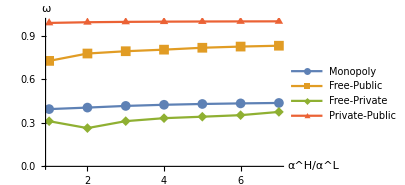

degreeoqtslope.png

```mathematica
middle=Grid[Transpose[Map[Flatten,Prepend[Take[-cqt,All,{8,8}],{{"sw","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}]]]];
ListLinePlot[middle[[1,2;;8,2;;8]],DataRange->{1,7},AxesLabel->{"Heterogeneity","Social Welfare"},PlotLegends->{"free-free","public-public","Stackelberg-private","Monopoly","free-public","free-private","private-public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{Heterogeneity,ω},Axes->{True,True},ImageSize->500];
somedayqt=Take[Map[Flatten,Prepend[Take[-cqt,All,{8,8}],{{"sw","free-free","public-public","Stackelberg-private","Monopoly","free-public","free-private","private-public"}}]],{2,8},{2,8}];
gooddayqt=Map[(#-#[[2]])/(#[[3]]-#[[2]])&,somedayqt]
nicedayqt=ListLinePlot[Transpose[gooddayqt[[All,4;;7]]],DataRange->{1,7},PlotLegends->{"Monopoly","Free-Public","Free-Private","Private-Public"},PlotMarkers->{Automatic, 10},PlotRange-> All,AxesLabel->{"α^H/α^L",ω},Axes->{True,True},ImageSize->300]
Export["degreeoqtslope.png",nicedayqt]
```

```mathematica
3897/7794
3494/6988
```

1/2

1/2

sw | price h | price h | price h | price h | price h | price h | price h
Stackelberg-private | 15.514 | 14.6606 | 14.1761 | 19.7018 | 19.6572 | 19.6279 | 19.6074
free-free | 10.9128 | 14.0307 | 15.5076 | 16.3692 | 16.9336 | 17.3321 | 17.6283
public-public | 10.9128 | 10.7877 | 10.8407 | 10.8987 | 10.9464 | 10.9843 | 11.0146
Monopoly | 22.244 | 22.322 | 22.4796 | 22.6045 | 22.6989 | 22.7714 | 22.8283
free-public | 8.97464 | 10.7029 | 11.7037 | 9.10475 | 9.47048 | 9.69849 | 9.74741
free-private | 14.1065 | 20.4828 | 23.2728 | 25.014 | 26.2089 | 26.961 | 27.1889
private-public | 12.2338 | 11.9316 | 11.8416 | 11.786 | 11.7422 | 11.7052 | 11.6732

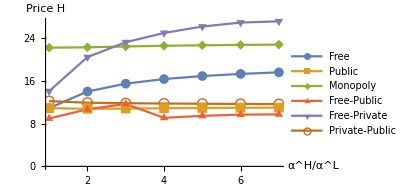

degreeoqtslopeph.png

```mathematica
middleph=Grid[Transpose[Map[Flatten,Prepend[Take[cqt,All,{11,11}],{{"ph","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}]]]]
nicedayqtph=ListLinePlot[middleph[[1,3;;8,2;;8]],DataRange->{1,7},PlotLegends->{"Free","Public","Monopoly","Free-Public","Free-Private","Private-Public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{"α^H/α^L","Price H"},Axes->{True,True},ImageSize->300]
Export["degreeoqtslopeph.png",nicedayqtph]
```

sw | price l | price l | price l | price l | price l | price l | price l
Stackelberg-private | 15.514 | 11.6107 | 9.36944 | 14.8749 | 14.204 | 13.7188 | 13.3519
free-free | 10.9128 | 7.01536 | 5.16921 | 4.0923 | 3.38673 | 2.88868 | 2.51834
public-public | 10.9128 | 7.31977 | 5.50347 | 4.40903 | 3.67765 | 3.1544 | 2.76151
Monopoly | 22.244 | 20.099 | 18.9938 | 18.3259 | 17.8797 | 17.5608 | 17.3216
free-public | 8.97464 | 5.48719 | 3.90383 | 2.27619 | 1.8941 | 1.56608 | 1.10331
free-private | 14.1065 | 10.2414 | 7.75761 | 6.25351 | 5.24179 | 4.51356 | 3.96386
private-public | 12.2338 | 8.58711 | 6.6636 | 5.46389 | 4.63927 | 4.03545 | 3.5732

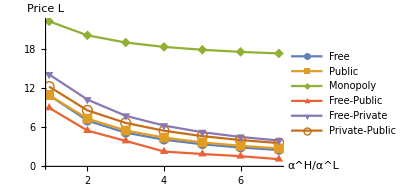

degreeoqtslopepl.png

```mathematica
middlepl=Grid[Transpose[Map[Flatten,Prepend[Take[cqt,All,{12,12}],{{"pl","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}]]]]
nicedayqtpl=ListLinePlot[middlepl[[1,3;;8,2;;8]],DataRange->{1,7},PlotLegends->{"Free","Public","Monopoly","Free-Public","Free-Private","Private-Public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{"α^H/α^L","Price L"},Axes->{True,True},ImageSize->300]
Export["degreeoqtslopepl.png",nicedayqtpl]
```

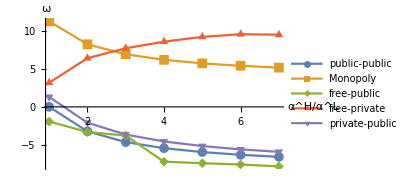

degreeoqtslopephd.png

```mathematica
somedayqtphd=Take[Map[Flatten,Prepend[Take[cqt,All,{11,11}],{{"sw","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}]],{2,8},{2,8}];
gooddayqtphd=Map[#-#[[2]]&,somedayqtphd];
nicedayqtphd=ListLinePlot[Transpose[gooddayqtphd[[All,3;;7]]],DataRange->{1,7},PlotLegends->{"public-public","Monopoly","free-public","free-private","private-public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{"α^H/α^L",ω},Axes->{True,True},ImageSize->300]
Export["degreeoqtslopephd.png",nicedayqtphd]
(*monopoly is bad for both high and low types, free is good for the low types and public is good for the high types. *)
```

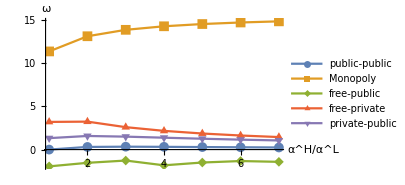

degreeoqtslopepld.png

```mathematica
somedayqtpld=Take[Map[Flatten,Prepend[Take[cqt,All,{12,12}],{{"sw","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}]],{2,8},{2,8}];
gooddayqtpld=Map[#-#[[2]]&,somedayqtpld];
nicedayqtpld=ListLinePlot[Transpose[gooddayqtpld[[All,3;;7]]],DataRange->{1,7},PlotLegends->{"public-public","Monopoly","free-public","free-private","private-public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{"α^H/α^L",ω},Axes->{True,True},ImageSize->300]
Export["degreeoqtslopepld.png",nicedayqtpld]
```

sw | nh1 | nh1 | nh1 | nh1 | nh1 | nh1 | nh1
Stackelberg-private | 9750.76 | 3912.78 | 4184.38 | 3538.53 | 3622.86 | 3682.09 | 3725.96
free-free | 9000. | 9000. | 9000. | 9000. | 9000. | 9000. | 9000.
public-public | 9000. | 4449.06 | 4646.24 | 4757.5 | 4829.06 | 4878.99 | 4915.81
Monopoly | 5251.71 | 2851.89 | 3034.58 | 3136.59 | 3201.68 | 3246.81 | 3279.95
free-public | 7401.57 | 0 | 0 | 5005.92 | 5033.43 | 5036.12 | 4976.46
free-private | 10610. | 0 | 0 | 0 | 0 | 0 | 0
private-public | 7689.08 | 4290.67 | 4507.64 | 4634.64 | 4718.87 | 4779.17 | 4824.62

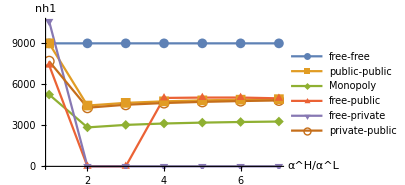

sw | nh2 | nh2 | nh2 | nh2 | nh2 | nh2 | nh2
Stackelberg-private | 337.81 | 7825.55 | 8368.76 | 7077.05 | 7245.73 | 7364.19 | 7451.92
free-free | 3000. | 3000. | 3000. | 3000. | 3000. | 3000. | 3000.
public-public | 3000. | 8898.12 | 9292.49 | 9515. | 9658.12 | 9757.97 | 9831.63
Monopoly | 2041.14 | 5703.79 | 6069.16 | 6273.17 | 6403.35 | 6493.63 | 6559.91
free-public | 5403.56 | 13382.4 | 13580.2 | 10011.8 | 10066.9 | 10135. | 10297.4
free-private | 63.3138 | 9319.71 | 8774.23 | 8408.8 | 8146.9 | 8000. | 8028.41
private-public | 3762.16 | 8581.33 | 9015.29 | 9269.28 | 9437.74 | 9558.33 | 9649.24

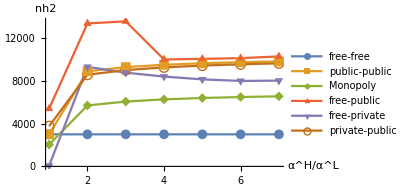

sw | nl1 | nl1 | nl1 | nl1 | nl1 | nl1 | nl1
Stackelberg-private | 0 | 7103.84 | 7679.1 | 8778.82 | 8758.8 | 8751.4 | 8749.41
free-free | 0 | 0 | 0 | 0 | 0 | 0 | 0
public-public | 0 | 4941.46 | 4935.72 | 4939.08 | 4944.05 | 4948.9 | 4953.23
Monopoly | 0 | 2483.74 | 2341.24 | 2262.57 | 2212.69 | 2178.23 | 2153.01
free-public | 0 | 7039.51 | 6796.87 | 0 | 0 | 0 | 0
free-private | 1024. | 13138.7 | 13506.6 | 13753.1 | 13929.7 | 14062.5 | 14166.
private-public | 0 | 3893.45 | 3989.16 | 4084.75 | 4168.85 | 4240.92 | 4302.52

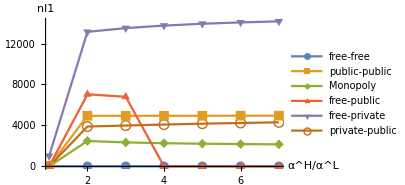

sw | nl2 | nl2 | nl2 | nl2 | nl2 | nl2 | nl2
Stackelberg-private | 12345.2 | 5244.83 | 4897.52 | 0 | 0 | 0 | 0
free-free | 15000. | 15000. | 15000. | 15000. | 15000. | 15000. | 15000.
public-public | 15000. | 9882.91 | 9871.43 | 9878.17 | 9888.1 | 9897.79 | 9906.47
Monopoly | 8462.29 | 4967.47 | 4682.48 | 4525.14 | 4425.38 | 4356.47 | 4306.01
free-public | 16118.2 | 8842.19 | 8933.21 | 16047.8 | 15861.2 | 15763.1 | 15816.4
free-private | 12133.3 | 0 | 0 | 0 | 0 | 0 | 0
private-public | 14237.8 | 10199.7 | 10148.6 | 10123.9 | 10108.5 | 10097.4 | 10088.9

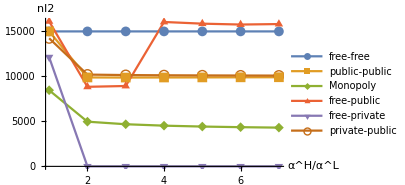

```mathematica
www=Grid[Transpose[Map[Flatten,Prepend[Take[cqt,All,{2,2}],{{"sw","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}]]]]
wwx=ListLinePlot[www[[1,3;;8,2;;8]],DataRange->{1,7},PlotLegends->{"free-free","public-public","Monopoly","free-public","free-private","private-public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{"α^H/α^L","nh1"},Axes->{True,True},ImageSize->300]
www=Grid[Transpose[Map[Flatten,Prepend[Take[cqt,All,{3,3}],{{"sw","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}]]]]
wwx=ListLinePlot[www[[1,3;;8,2;;8]],DataRange->{1,7},PlotLegends->{"free-free","public-public","Monopoly","free-public","free-private","private-public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{"α^H/α^L","nh2"},Axes->{True,True},ImageSize->300]
www=Grid[Transpose[Map[Flatten,Prepend[Take[cqt,All,{4,4}],{{"sw","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}]]]]
wwx=ListLinePlot[www[[1,3;;8,2;;8]],DataRange->{1,7},PlotLegends->{"free-free","public-public","Monopoly","free-public","free-private","private-public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{"α^H/α^L","nl1"},Axes->{True,True},ImageSize->300]
www=Grid[Transpose[Map[Flatten,Prepend[Take[cqt,All,{5,5}],{{"sw","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}]]]]
wwx=ListLinePlot[www[[1,3;;8,2;;8]],DataRange->{1,7},PlotLegends->{"free-free","public-public","Monopoly","free-public","free-private","private-public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{"α^H/α^L","nl2"},Axes->{True,True},ImageSize->300]
```

sw | tau1 | tau1 | tau1 | tau1 | tau1 | tau1 | tau1
Stackelberg-private | 3.69092 | 3.0234 | 2.55556 | 9.27421 | 9.54476 | 9.7281 | 9.86111
free-free | 0 | 0 | 0 | 0 | 0 | 0 | 0
public-public | 0 | 0 | 0 | 0 | 0 | 0 | 0
Monopoly | 15.8761 | 15.9399 | 15.9061 | 15.8709 | 15.8422 | 15.8196 | 15.8014
free-public | 0 | 0 | 0 | 0 | 0 | 0 | 0
free-private | 0 | 0 | 0 | 0 | 0 | 0 | 0
private-public | 2.91052 | 2.20772 | 1.7834 | 1.49919 | 1.29479 | 1.14033 | 1.01929

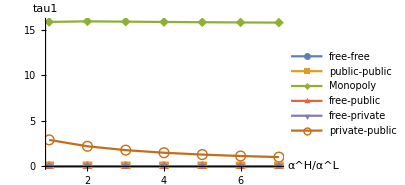

sw | tau2 | tau2 | tau2 | tau2 | tau2 | tau2 | tau2
Stackelberg-private | 7.82473 | 6.5166 | 5.55964 | 13.2659 | 12.8407 | 12.537 | 12.3093
free-free | 0 | 0 | 0 | 0 | 0 | 0 | 0
public-public | 0 | 0 | 0 | 0 | 0 | 0 | 0
Monopoly | 15.8761 | 15.9399 | 15.9061 | 15.8709 | 15.8422 | 15.8196 | 15.8014
free-public | -4.07329 | -3.17468 | -2.56154 | -3.64847 | -2.98431 | -2.5901 | -2.55021
free-private | 6.71214 | 13.2182 | 15.7135 | 17.3671 | 18.5447 | 19.2579 | 19.3262
private-public | 1.32099 | 1.26735 | 1.16013 | 1.05486 | 0.961619 | 0.881054 | 0.811691

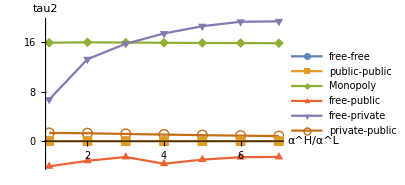

```mathematica
www=Grid[Transpose[Map[Flatten,Prepend[Take[cqt,All,{9,9}],{{"sw","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}]]]]
wwx=ListLinePlot[www[[1,3;;8,2;;8]],DataRange->{1,7},PlotLegends->{"free-free","public-public","Monopoly","free-public","free-private","private-public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{"α^H/α^L","tau1"},Axes->{True,True},ImageSize->300]
www=Grid[Transpose[Map[Flatten,Prepend[Take[cqt,All,{10,10}],{{"sw","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}]]]]
wwx=ListLinePlot[www[[1,3;;8,2;;8]],DataRange->{1,7},PlotLegends->{"free-free","public-public","Monopoly","free-public","free-private","private-public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{"α^H/α^L","tau2"},Axes->{True,True},ImageSize->300]
```

## Backup

```mathematica
Clear[dgr,nh1,nh2,nl1,nl2,pi1,pi2,sw,eh,el,c,ph,pl,csh,csl,m2,tau1,tau2,ft1,ftp1,s,sa,s1,nh,nl,g,alpha, beta,gamma, h,l,ah,al,bh,bl,idc,min,max,ss,list,a,rfstbp]
s=12000;
sa=1/3;
s1=s*sa; 
nh=12000;
nl=15000;
g=sa/(1-sa); 
alpha=90/(4+5 dgr);
beta=39/64*alpha;(*marginal schedule delay cost of arriving early*)
gamma=1521/10/64*alpha;(*marginal schedule delay cost of arriving late*)
h=beta*gamma/(beta+gamma)/s1; (*marginal congestion cost for high type*)
l=dgr*h;(*marginal congestion cost for low type,9/10*h*)
bh=41067/17059840;
bl=369603/213248000;
ah=bh*nh+h*(nh+nl)*sa;
al=bl*nl+l*(nh+nl)*sa;
ft1[tau2_]:=(*ft1 calculates the best response for private supplier on link 1*)
Module[{nh1,nh2,nl1,nl2,pi1,pi2,sw,eh,el,c,ph,pl,csh,csl,m2,tau1},
pi1=-tau1*(nh1+nl1);
pi2=-tau2*(nh2+nl2);
sw=-ah*(nh1+nh2)+bh*(nh1+nh2)^2/2-al*(nl1+nl2)+bl*(nl1+nl2)^2/2+h*(nh1+nl1)*nh1+l*(nh1+nl1)*nl1+h*g*(nh2+nl2)*nh2+l*g*(nh2+nl2)*nl2;
csh=ah*(nh1+nh2)-bh*(nh1+nh2)^2/2-(h*nh1+h*nl1+tau1)*nh1-(h*g*nh2+h*g*nl2+tau2)*nh2;
csl=al*(nl1+nl2)-bl*(nl1+nl2)^2/2-(l*nh1+l*nl1+tau1)*nl1-(l*g*nh2+l*g*nl2+tau2)*nl2;
ph=ah-bh*(nh1+nh2);
pl=al-bl*(nl1+nl2);
m2=Minimize[pi1,
{nh1*(ah-bh*(nh1+nh2)-h*nh1-h*nl1-tau1)==0,nh2*(ah-bh*(nh1+nh2)-h*g*nh2-h*g*nl2-tau2)==0,nl1*(al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1)==0,nl2*(al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2)==0,ah-bh*(nh1+nh2)-h*nh1-h*nl1-tau1≤0,ah-bh*(nh1+nh2)-h*g*nh2-h*g*nl2-tau2≤0,al-bl*(nl1+nl2)-l*nh1-l*nl1-tau1≤0,al-bl*(nl1+nl2)-l*g*nh2-l*g*nl2-tau2≤0,
nh1≥0,nh2≥0,nl1≥0,nl2≥0},{nh1,nh2,nl1,nl2,tau1}][[2]];
{nh1,nh2,nl1,nl2,pi1,pi2,sw,tau1,tau2,ph,pl,csh,csl}/.m2
];
```

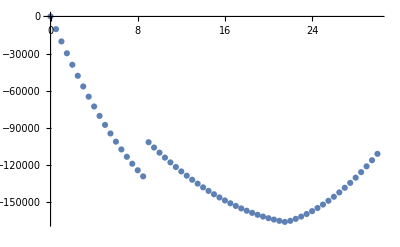

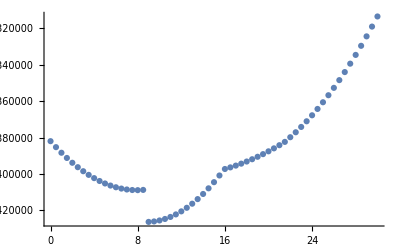

```mathematica
dgr=2/10;
tu2=ListPlot[Table[{i,ft1[i][[6]]},{i,0,30,1/2}]]
tu2p=ListPlot[Table[{i,ft1[i][[7]]},{i,0,30,1/2}]]
```

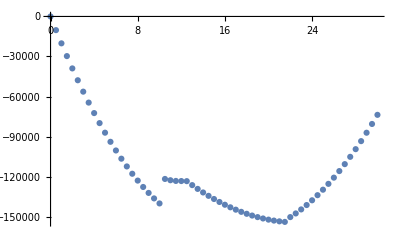

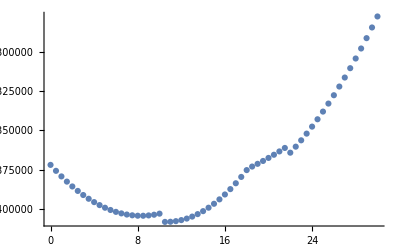

```mathematica
dgr=4/10;
tu4=ListPlot[Table[{i,ft1[i][[6]]},{i,0,30,1/2}]]
tu4p=ListPlot[Table[{i,ft1[i][[7]]},{i,0,30,1/2}]]
```

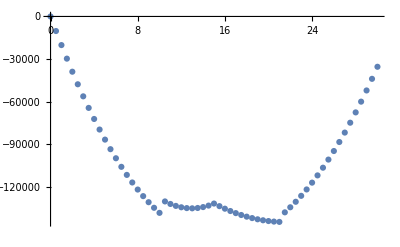

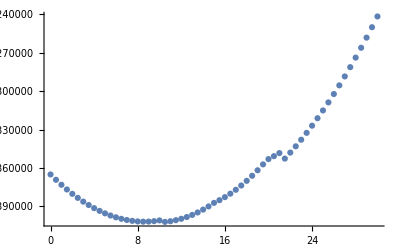

```mathematica
dgr=6/10;
tu6=ListPlot[Table[{i,ft1[i][[6]]},{i,0,30,1/2}]]
tu6p=ListPlot[Table[{i,ft1[i][[7]]},{i,0,30,1/2}]]
```

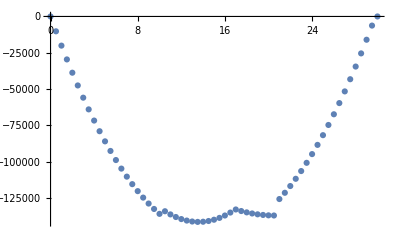

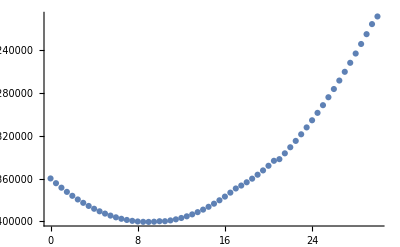

```mathematica
dgr=8/10;
tu8=ListPlot[Table[{i,ft1[i][[6]]},{i,0,30,1/2}]]
tu8p=ListPlot[Table[{i,ft1[i][[7]]},{i,0,30,1/2}]]
```

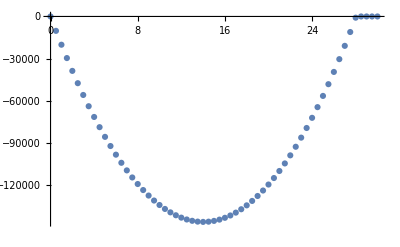

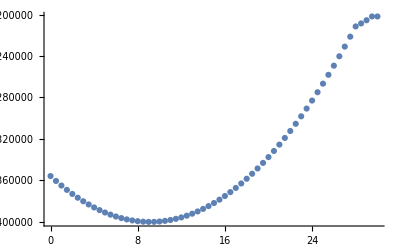

```mathematica
dgr=10/10;
tu10=ListPlot[Table[{i,ft1[i][[6]]},{i,0,30,1/2}]]
tu10p=ListPlot[Table[{i,ft1[i][[7]]},{i,0,30,1/2}]]
```

```mathematica
N[519555/368307]
```

1.41066

## Result

```mathematica
SetDirectory[NotebookDirectory[]];
cft=Import["degreeftslope.xls"];
cqt=Import["degreeqetslope.xls"];
```

```mathematica
(*Plot the traffic flows in the flat toll regime. *)
www=Grid[Transpose[Map[Flatten,Prepend[Take[cft,All,{2,2}],{{"flat","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}]]]]
wwx=ListLinePlot[www[[1,3;;8,2;;8]],DataRange->{1,7},PlotLegends->{"free-free","public-public","Monopoly","free-public","free-private","private-public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{"α^H/α^L","nh1"},Axes->{True,True},ImageSize->300]
www=Grid[Transpose[Map[Flatten,Prepend[Take[cft,All,{3,3}],{{"flat","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}]]]]
wwx=ListLinePlot[www[[1,3;;8,2;;8]],DataRange->{1,7},PlotLegends->{"free-free","public-public","Monopoly","free-public","free-private","private-public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{"α^H/α^L","nh2"},Axes->{True,True},ImageSize->300]
www=Grid[Transpose[Map[Flatten,Prepend[Take[cft,All,{4,4}],{{"flat","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}]]]]
wwx=ListLinePlot[www[[1,3;;8,2;;8]],DataRange->{1,7},PlotLegends->{"free-free","public-public","Monopoly","free-public","free-private","private-public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{"α^H/α^L","nl1"},Axes->{True,True},ImageSize->300]
www=Grid[Transpose[Map[Flatten,Prepend[Take[cft,All,{5,5}],{{"flat","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}]]]]
wwx=ListLinePlot[www[[1,3;;8,2;;8]],DataRange->{1,7},PlotLegends->{"free-free","public-public","Monopoly","free-public","free-private","private-public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{"α^H/α^L","nl2"},Axes->{True,True},ImageSize->300]
```

flat | nh1 | nh1 | nh1 | nh1 | nh1 | nh1 | nh1
Stackelberg-private | 7250.97 | 0. | 0. | 0. | 0. | 0. | 0.
free-free | 9000. | 9000. | 9000. | 9000. | 9000. | 9000. | 9000.
public-public | 6996.96 | 0. | 0. | 0. | 0. | 0. | 0.
Monopoly | 4500. | 0. | 0. | 0. | 122.591 | 204.082 | 258.488
free-public | 10344. | 0. | 0. | 0. | 0. | 0. | 0.
free-private | 8988.8 | 220.989 | 0. | 0. | 0. | 0. | 0.
private-public | 6355.02 | 0. | 0. | 0. | 0. | 0. | 0.

-Graphics-

flat | nh2 | nh2 | nh2 | nh2 | nh2 | nh2 | nh2
Stackelberg-private | 837.492 | 6933.25 | 7218.48 | 7388.74 | 7500.59 | 7579.29 | 7637.52
free-free | 3000. | 3000. | 3000. | 3000. | 3000. | 3000. | 3000.
public-public | 2487.59 | 10120.8 | 10726.1 | 10708.9 | 10683.9 | 10666.7 | 10654.1
Monopoly | 1848.84 | 6733.81 | 7107.99 | 7336.1 | 7274.39 | 7226.51 | 7194.3
free-public | 979.029 | 11783.2 | 10748.5 | 10708.9 | 10683.9 | 10666.7 | 10654.1
free-private | 953.677 | 9000. | 8774.23 | 8408.8 | 8146.9 | 7950. | 7796.57
private-public | 2776.92 | 9753.13 | 10345.7 | 10630.1 | 10683.9 | 10666.7 | 10654.1

-Graphics-

flat | nl1 | nl1 | nl1 | nl1 | nl1 | nl1 | nl1
Stackelberg-private | 0. | 6569.34 | 6753.29 | 6876.53 | 6964.85 | 7031.25 | 7082.99
free-free | 0. | 0. | 0. | 0. | 0. | 0. | 0.
public-public | 0. | 8777.83 | 10766.3 | 11386.6 | 11821. | 12162.2 | 12437.2
Monopoly | 0. | 6569.34 | 6644.16 | 6757.17 | 6821.14 | 6874.57 | 6919.89
free-public | 0. | 11827.4 | 13506.6 | 13753.1 | 13929.7 | 14062.5 | 14166.
free-private | 4096. | 13070.1 | 13506.6 | 13753.1 | 13929.7 | 14062.5 | 14166.
private-public | 0. | 8103.27 | 10069.3 | 10197.1 | 9995.18 | 9753.09 | 9572.85

-Graphics-

flat | nl2 | nl2 | nl2 | nl2 | nl2 | nl2 | nl2
Stackelberg-private | 9567.31 | 0. | 0. | 0. | 0. | 0. | 0.
free-free | 15000. | 15000. | 15000. | 15000. | 15000. | 15000. | 15000.
public-public | 11506.3 | 2374.39 | 80.537 | 0. | 0. | 0. | 0.
Monopoly | 7151.16 | 0. | 0. | 0. | 0. | 0. | 0.
free-public | 14059.8 | 1901.05 | 0. | 0. | 0. | 0. | 0.
free-private | 8046.32 | 0. | 0. | 0. | 0. | 0. | 0.
private-public | 11016.6 | 2479.09 | 144.549 | 0. | 0. | 0. | 0.

-Graphics-

```mathematica
(*Plot Traffic flows in queue-eliminating toll*)
www=Grid[Transpose[Map[Flatten,Prepend[Take[cqt,All,{2,2}],{{"QT","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}]]]]
wwx=ListLinePlot[www[[1,3;;8,2;;8]],DataRange->{1,7},PlotLegends->{"free-free","public-public","Monopoly","free-public","free-private","private-public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{"α^H/α^L","nh1"},Axes->{True,True},ImageSize->300]
www=Grid[Transpose[Map[Flatten,Prepend[Take[cqt,All,{3,3}],{{"QT","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}]]]]
wwx=ListLinePlot[www[[1,3;;8,2;;8]],DataRange->{1,7},PlotLegends->{"free-free","public-public","Monopoly","free-public","free-private","private-public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{"α^H/α^L","nh2"},Axes->{True,True},ImageSize->300]
www=Grid[Transpose[Map[Flatten,Prepend[Take[cqt,All,{4,4}],{{"QT","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}]]]]
wwx=ListLinePlot[www[[1,3;;8,2;;8]],DataRange->{1,7},PlotLegends->{"free-free","public-public","Monopoly","free-public","free-private","private-public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{"α^H/α^L","nl1"},Axes->{True,True},ImageSize->300]
www=Grid[Transpose[Map[Flatten,Prepend[Take[cqt,All,{5,5}],{{"QT","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}]]]]
wwx=ListLinePlot[www[[1,3;;8,2;;8]],DataRange->{1,7},PlotLegends->{"free-free","public-public","Monopoly","free-public","free-private","private-public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{"α^H/α^L","nl2"},Axes->{True,True},ImageSize->300]
```

QT | nh1 | nh1 | nh1 | nh1 | nh1 | nh1 | nh1
Stackelberg-private | 9750.76 | 3912.78 | 4184.38 | 3538.53 | 3622.86 | 3682.09 | 3725.96
free-free | 9000. | 9000. | 9000. | 9000. | 9000. | 9000. | 9000.
public-public | 9000. | 4449.06 | 4646.24 | 4757.5 | 4829.06 | 4878.99 | 4915.81
Monopoly | 5251.71 | 2851.89 | 3034.58 | 3136.59 | 3201.68 | 3246.81 | 3279.95
free-public | 7401.57 | 0. | 0. | 5005.92 | 5033.43 | 5036.12 | 4976.46
free-private | 10610. | 0. | 0. | 0. | 0. | 0. | 0.
private-public | 7689.08 | 4290.67 | 4507.64 | 4634.64 | 4718.87 | 4779.17 | 4824.62

-Graphics-

QT | nh2 | nh2 | nh2 | nh2 | nh2 | nh2 | nh2
Stackelberg-private | 337.81 | 7825.55 | 8368.76 | 7077.05 | 7245.73 | 7364.19 | 7451.92
free-free | 3000. | 3000. | 3000. | 3000. | 3000. | 3000. | 3000.
public-public | 3000. | 8898.12 | 9292.49 | 9515. | 9658.12 | 9757.97 | 9831.63
Monopoly | 2041.14 | 5703.79 | 6069.16 | 6273.17 | 6403.35 | 6493.63 | 6559.91
free-public | 5403.56 | 13382.4 | 13580.2 | 10011.8 | 10066.9 | 10135. | 10297.4
free-private | 63.3138 | 9319.71 | 8774.23 | 8408.8 | 8146.9 | 8000. | 8028.41
private-public | 3762.16 | 8581.33 | 9015.29 | 9269.28 | 9437.74 | 9558.33 | 9649.24

-Graphics-

QT | nl1 | nl1 | nl1 | nl1 | nl1 | nl1 | nl1
Stackelberg-private | 0. | 7103.84 | 7679.1 | 8778.82 | 8758.8 | 8751.4 | 8749.41
free-free | 0. | 0. | 0. | 0. | 0. | 0. | 0.
public-public | 0. | 4941.46 | 4935.72 | 4939.08 | 4944.05 | 4948.9 | 4953.23
Monopoly | 0. | 2483.74 | 2341.24 | 2262.57 | 2212.69 | 2178.23 | 2153.01
free-public | 0. | 7039.51 | 6796.87 | 0. | 0. | 0. | 0.
free-private | 1024. | 13138.7 | 13506.6 | 13753.1 | 13929.7 | 14062.5 | 14166.
private-public | 0. | 3893.45 | 3989.16 | 4084.75 | 4168.85 | 4240.92 | 4302.52

-Graphics-

QT | nl2 | nl2 | nl2 | nl2 | nl2 | nl2 | nl2
Stackelberg-private | 12345.2 | 5244.83 | 4897.52 | 0. | 0. | 0. | 0.
free-free | 15000. | 15000. | 15000. | 15000. | 15000. | 15000. | 15000.
public-public | 15000. | 9882.91 | 9871.43 | 9878.17 | 9888.1 | 9897.79 | 9906.47
Monopoly | 8462.29 | 4967.47 | 4682.48 | 4525.14 | 4425.38 | 4356.47 | 4306.01
free-public | 16118.2 | 8842.19 | 8933.21 | 16047.8 | 15861.2 | 15763.1 | 15816.4
free-private | 12133.3 | 0. | 0. | 0. | 0. | 0. | 0.
private-public | 14237.8 | 10199.7 | 10148.6 | 10123.9 | 10108.5 | 10097.4 | 10088.9

-Graphics-

Flat | price h | price h | price h | price h | price h | price h | price h
Stackelberg-private | 20.3288 | 26.2276 | 27.0179 | 27.4696 | 27.7648 | 27.9737 | 28.1298
free-free | 10.9128 | 14.0307 | 15.5076 | 16.3692 | 16.9336 | 17.3321 | 17.6283
public-public | 16.9681 | 18.5543 | 18.5743 | 19.4773 | 20.1019 | 20.5417 | 20.8682
Monopoly | 24.5164 | 26.7077 | 27.2839 | 27.5963 | 28.0142 | 28.3317 | 28.5746
free-public | 12.5424 | 14.5526 | 18.5204 | 19.4773 | 20.1019 | 20.5417 | 20.8682
free-private | 15.8657 | 20.7205 | 23.2728 | 25.014 | 26.2089 | 27.0814 | 27.747
private-public | 17.8169 | 19.4395 | 19.4898 | 19.667 | 20.1019 | 20.5417 | 20.8682

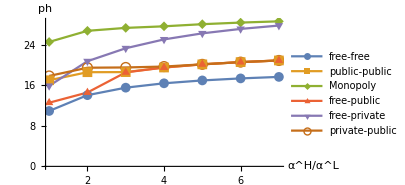

Flat | price l | price l | price l | price l | price l | price l | price l
Stackelberg-private | 20.3288 | 21.6274 | 19.4625 | 18.172 | 17.3133 | 16.7002 | 16.2402
free-free | 10.9128 | 7.01536 | 5.16921 | 4.0923 | 3.38673 | 2.88868 | 2.51834
public-public | 16.9681 | 13.6844 | 12.3674 | 10.355 | 8.89657 | 7.80724 | 6.96022
Monopoly | 24.5164 | 21.6274 | 19.6516 | 18.3788 | 17.5624 | 16.9717 | 16.5228
free-public | 12.5424 | 9.21926 | 7.75761 | 6.25351 | 5.24179 | 4.51356 | 3.96386
free-private | 15.8657 | 10.3602 | 7.75761 | 6.25351 | 5.24179 | 4.51356 | 3.96386
private-public | 17.8169 | 14.672 | 13.4647 | 12.4167 | 12.0611 | 11.9827 | 11.9247

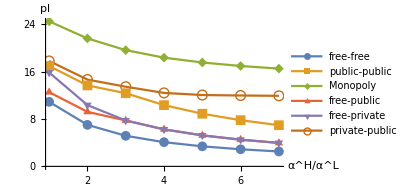

```mathematica
(*Plot prices in flat toll*)www=Grid[Transpose[Map[Flatten,Prepend[Take[cft,All,{11,11}],{{"Flat","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}]]]]
wwx=ListLinePlot[www[[1,3;;8,2;;8]],DataRange->{1,7},PlotLegends->{"free-free","public-public","Monopoly","free-public","free-private","private-public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{"α^H/α^L","ph"},Axes->{True,True},ImageSize->300]
www=Grid[Transpose[Map[Flatten,Prepend[Take[cft,All,{12,12}],{{"Flat","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}]]]]
wwx=ListLinePlot[www[[1,3;;8,2;;8]],DataRange->{1,7},PlotLegends->{"free-free","public-public","Monopoly","free-public","free-private","private-public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{"α^H/α^L","pl"},Axes->{True,True},ImageSize->300]
```

QT | price h | price h | price h | price h | price h | price h | price h
Stackelberg-private | 15.514 | 14.6606 | 14.1761 | 19.7018 | 19.6572 | 19.6279 | 19.6074
free-free | 10.9128 | 14.0307 | 15.5076 | 16.3692 | 16.9336 | 17.3321 | 17.6283
public-public | 10.9128 | 10.7877 | 10.8407 | 10.8987 | 10.9464 | 10.9843 | 11.0146
Monopoly | 22.244 | 22.322 | 22.4796 | 22.6045 | 22.6989 | 22.7714 | 22.8283
free-public | 8.97464 | 10.7029 | 11.7037 | 9.10475 | 9.47048 | 9.69849 | 9.74741
free-private | 14.1065 | 20.4828 | 23.2728 | 25.014 | 26.2089 | 26.961 | 27.1889
private-public | 12.2338 | 11.9316 | 11.8416 | 11.786 | 11.7422 | 11.7052 | 11.6732

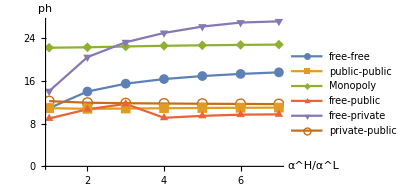

QT | price l | price l | price l | price l | price l | price l | price l
Stackelberg-private | 15.514 | 11.6107 | 9.36944 | 14.8749 | 14.204 | 13.7188 | 13.3519
free-free | 10.9128 | 7.01536 | 5.16921 | 4.0923 | 3.38673 | 2.88868 | 2.51834
public-public | 10.9128 | 7.31977 | 5.50347 | 4.40903 | 3.67765 | 3.1544 | 2.76151
Monopoly | 22.244 | 20.099 | 18.9938 | 18.3259 | 17.8797 | 17.5608 | 17.3216
free-public | 8.97464 | 5.48719 | 3.90383 | 2.27619 | 1.8941 | 1.56608 | 1.10331
free-private | 14.1065 | 10.2414 | 7.75761 | 6.25351 | 5.24179 | 4.51356 | 3.96386
private-public | 12.2338 | 8.58711 | 6.6636 | 5.46389 | 4.63927 | 4.03545 | 3.5732

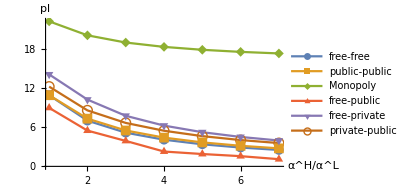

```mathematica
(*Plot prices in queue-eliminating toll*)
www=Grid[Transpose[Map[Flatten,Prepend[Take[cqt,All,{11,11}],{{"QT","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}]]]]
wwx=ListLinePlot[www[[1,3;;8,2;;8]],DataRange->{1,7},PlotLegends->{"free-free","public-public","Monopoly","free-public","free-private","private-public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{"α^H/α^L","ph"},Axes->{True,True},ImageSize->300]
www=Grid[Transpose[Map[Flatten,Prepend[Take[cqt,All,{12,12}],{{"QT","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}]]]]
wwx=ListLinePlot[www[[1,3;;8,2;;8]],DataRange->{1,7},PlotLegends->{"free-free","public-public","Monopoly","free-public","free-private","private-public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{"α^H/α^L","pl"},Axes->{True,True},ImageSize->300]
```

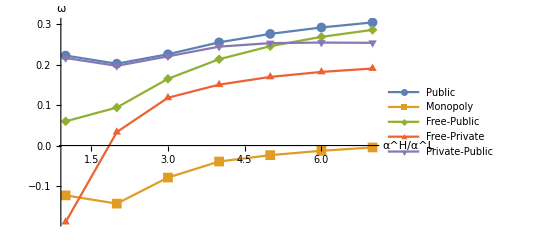

degreeoftslope.eps

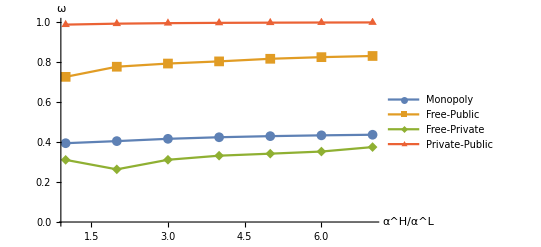

degreeoqtslope.eps

for flat toll: private-public's efficiency is increasing slowly and even decreases, because separating equilibrium give local monopoly power. Should be similar for free-private. 
for queue-eliminating toll: stable efficiency, because always enough competition? At least for private-public yes. for free-private not so?

```mathematica
(*Plot efficiency of both tolls*)
Clear[middle];
middle=Prepend[Take[-cft,All,{8,8}],{{"sw","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}];
middle=Map[Flatten,Join[middle,Take[-cqt,All,{8,8}]]];
ListLinePlot[Grid[Transpose[middle]][[1,2;;8,2;;8]],DataRange->{1,7},AxesLabel->{"Heterogeneity","Social Welfare"},PlotLegends->{"Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{Heterogeneity,ω},Axes->{True,True},ImageSize->500];
ListLinePlot[Grid[Transpose[middle]][[1,2;;8,9;;15]],DataRange->{1,7},AxesLabel->{"Heterogeneity","Social Welfare"},PlotLegends->{"Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{Heterogeneity,ω},Axes->{True,True},ImageSize->500];someday=Take[middle,{2,15},{2,8}];
someday[[1;;7,2]]=someday[[8;;14,3]];
someday[[8;;14,2]]=someday[[8;;14,3]];
goodday=Map[(#-368307)/(#[[2]]-368307)&,someday];
nicedayft=ListLinePlot[Transpose[goodday[[1;;7,3;;7]]],DataRange->{1,7},PlotLegends->{"Public","Monopoly","Free-Public","Free-Private","Private-Public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{"α^H/α^L",ω},Axes->{True,True},ImageSize->400]
Export["degreeoftslope.eps",nicedayft]
nicedayqt=ListLinePlot[Transpose[goodday[[8;;14,4;;7]]],DataRange->{1,7},PlotLegends->{"Monopoly","Free-Public","Free-Private","Private-Public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{"α^H/α^L",ω},Axes->{True,True},ImageSize->400]
Export["degreeoqtslope.eps",nicedayqt]
Print["for flat toll: private-public's efficiency is increasing slowly and even decreases, because separating equilibrium give local monopoly power. Should be similar for free-private. 
for queue-eliminating toll: stable efficiency, because always enough competition? At least for private-public yes. for free-private not so?"]
```

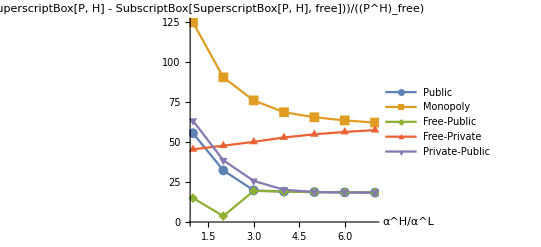

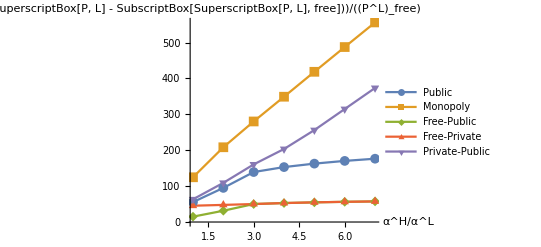

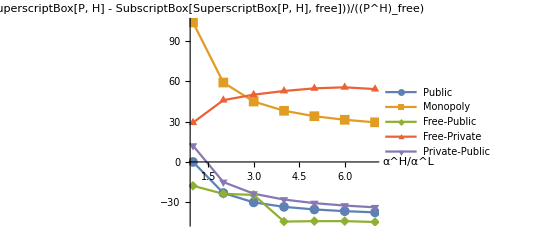

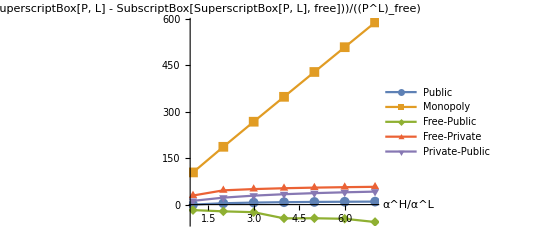

```mathematica
middle=Map[Flatten,Prepend[Take[cft,All,{11,11}],{{"ph","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}]];
middleph=Grid[Transpose[Map[(#-#[[3]])/#[[3]]*100&,middle]]];
nicedayftph=ListLinePlot[middleph[[1,4;;8,2;;8]],DataRange->{1,7},PlotLegends->{"Public","Monopoly","Free-Public","Free-Private","Private-Public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{"α^H/α^L","(100 (SuperscriptBox[P, H] - SubscriptBox[SuperscriptBox[P, H], free]))/((P^H)_free)"},Axes->{True,True},ImageSize->400]
Export["degreeoftslopeph.eps",nicedayftph];
middle=Map[Flatten,Prepend[Take[cft,All,{12,12}],{{"pl","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}]];
middlepl=Grid[Transpose[Map[(#-#[[3]])/#[[3]]*100&,middle]]];
nicedayftpl=ListLinePlot[middlepl[[1,4;;8,2;;8]],DataRange->{1,7},PlotLegends->{"Public","Monopoly","Free-Public","Free-Private","Private-Public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{"α^H/α^L","(100 (SuperscriptBox[P, L] - SubscriptBox[SuperscriptBox[P, L], free]))/((P^L)_free)"},Axes->{True,True},ImageSize->400]
Export["degreeoftslopepl.eps",nicedayftpl];
middle=Map[Flatten,Prepend[Take[cqt,All,{11,11}],{{"ph","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}]];
middleph=Grid[Transpose[Map[(#-#[[3]])/#[[3]]*100&,middle]]];
nicedayqtph=ListLinePlot[middleph[[1,4;;8,2;;8]],DataRange->{1,7},PlotLegends->{"Public","Monopoly","Free-Public","Free-Private","Private-Public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{"α^H/α^L","(100 (SuperscriptBox[P, H] - SubscriptBox[SuperscriptBox[P, H], free]))/((P^H)_free)"},Axes->{True,True},ImageSize->400]
Export["degreeoqtslopeph.eps",nicedayqtph];
middle=Map[Flatten,Prepend[Take[cqt,All,{12,12}],{{"pl","Stackelberg-private","free-free","public-public","Monopoly","free-public","free-private","private-public"}}]];
middlepl=Grid[Transpose[Map[(#-#[[3]])/#[[3]]*100&,middle]]];
nicedayqtpl=ListLinePlot[middlepl[[1,4;;8,2;;8]],DataRange->{1,7},PlotLegends->{"Public","Monopoly","Free-Public","Free-Private","Private-Public"},PlotMarkers->{Automatic, 10},PlotRange->All,AxesLabel->{"α^H/α^L","(100 (SuperscriptBox[P, L] - SubscriptBox[SuperscriptBox[P, L], free]))/((P^L)_free)"},Axes->{True,True},ImageSize->400]
Export["degreeoqtslopepl.eps",nicedayqtpl];
```

# Intuition

```mathematica
Clear[a,b,n,nf,np,nm]
(*sw*)a*n-b/2*n*n-d*n*n;
(*profit*)a*n-b*n*n-d*n*n;
(*free*)nf=n/.Solve[a-b*n-d*n==0,{n}][[1]];
Simplify[a-b*nf]
(*public*)np=n/.Solve[a-b*n-2d*n==0,{n}][[1]];
Simplify[a-b*np]
(*monopoly*)nm=n/.Solve[a-2*b*n-2*d*n==0,{n}][[1]];
Simplify[a-b*nm]
(*percentage price public*)Simplify[(a-b*np-d*nf)/(d*nf)]
(*percentage price monopoly*)Simplify[(a-b*nm-d*nf)/(d*nf)]
Print["b is the same, as \delta increases, the percentage change in price decreases. Since delta increases in high type and decreases in low types. d increases, n decreases, so prices increases for all three regimes. d increases, n decreases, so price in total increases. However, as d increases a little, n decreases a little, so price increases a little. The larger the delta, the higher the price. but the percentage change is lower..."]
```

(a d)/(b+d)

(2 a d)/(b+2 d)

a-(a b)/(2 (b+d))

b/(b+2 d)

b/(2 d)

b is the same, as \delta increases, the percentage change in price decreases. Since delta increases in high type and decreases in low types. d increases, n decreases, so prices increases for all three regimes. d increases, n decreases, so price in total increases. However, as d increases a little, n decreases a little, so price increases a little. The larger the delta, the higher the price. but the percentage change is lower...

# New

```mathematica
(*We want to prove for any demand function with fh''[nh1+nh2]<0 and fl''[nh1+nh2]<0, i.e. decreasing demand for higher prices, the solution is global optimal. 
sw is the social welfare, fh(fl) is the consumer surplus of high(low) types, s1 is normalized to 1*)
Clear[sw,dh,dl,nh1,nh2,nl1,nl2,fh,fl,nm,s1,s2,a,b]
sw=fh[nh1+nh2]+fl[nl1+nl2]-dh*nh1/2*nh1/s1-dl(nh1+nl1/2)*nl1/s1-dh*nh2/2*nh2/s2-dl*(nh2+nl2/2)*nl2/s2;
s1=1;
s2=b;
```

```mathematica
(*check hessian is negative definite. nm is the hessian matrix, we check the principle minors are of the following signs: -,+,-,+.*)
D[sw,{{nh1,nh2,nl1,nl2}}];
nm=D[sw,{{{nh1,nh2,nl1,nl2}},2}][[1]];
Simplify[Det[Take[nm,{1,1},{1,1}]]/.{dh->a*dl}]
Simplify[Det[Take[nm,{1,2},{1,2}]]/.{dh->a*dl}]
Simplify[Det[Take[nm,{1,3},{1,3}]]/.{dh->a*dl}]
Simplify[Det[Take[nm,{1,4},{1,4}]]/.{dh->a*dl}]
```

-a dl+fh''[nh1+nh2]

(a dl (a dl-(1+b) fh''[nh1+nh2]))/b

(dl (a dl (dl-a dl+a fl''[nl1+nl2])+fh''[nh1+nh2] ((a-b+a b) dl-a (1+b) fl''[nl1+nl2])))/b

1/b^2(-1+a) dl^2 ((1+b) fh''[nh1+nh2] (-dl+(1+b) fl''[nl1+nl2])+dl ((-1+a) dl-a (1+b) fl''[nl1+nl2]))

```mathematica
Solve[x^12==0.7,x]
```

{{x→-0.970714},{x→-0.840663-0.485357 ⅈ},{x→-0.840663+0.485357 ⅈ},{x→-0.485357-0.840663 ⅈ},{x→-0.485357+0.840663 ⅈ},{x→0.-0.970714 ⅈ},{x→0.+0.970714 ⅈ},{x→0.485357-0.840663 ⅈ},{x→0.485357+0.840663 ⅈ},{x→0.840663-0.485357 ⅈ},{x→0.840663+0.485357 ⅈ},{x→0.970714}}

```mathematica
0.97^12
```

0.693842

```mathematica
Solve[x^12==0.4,x]
```

{{x→-0.926485},{x→-0.802359-0.463242 ⅈ},{x→-0.802359+0.463242 ⅈ},{x→-0.463242-0.802359 ⅈ},{x→-0.463242+0.802359 ⅈ},{x→0.-0.926485 ⅈ},{x→0.+0.926485 ⅈ},{x→0.463242-0.802359 ⅈ},{x→0.463242+0.802359 ⅈ},{x→0.802359-0.463242 ⅈ},{x→0.802359+0.463242 ⅈ},{x→0.926485}}

```mathematica
0.93^12
```

0.418596

```mathematica
Solve[x^12==0.1,x]
```

{{x→-0.825404},{x→-0.714821-0.412702 ⅈ},{x→-0.714821+0.412702 ⅈ},{x→-0.412702-0.714821 ⅈ},{x→-0.412702+0.714821 ⅈ},{x→0.-0.825404 ⅈ},{x→0.+0.825404 ⅈ},{x→0.412702-0.714821 ⅈ},{x→0.412702+0.714821 ⅈ},{x→0.714821-0.412702 ⅈ},{x→0.714821+0.412702 ⅈ},{x→0.825404}}